# A mathematical model for universal semantics (Text mining in Spanish)

### Weinan E and Yajun Zhou

## Introduction

Accompanying the topic extraction and word translation sections in [1], this Mathematica Notebook file is optimized for v11.0, and it will also run on v10.3 and v10.4. Earlier versions of Mathematica do not contain certain text analysis functionalities required for this program.

Unless explicitly stated otherwise, all the routines (word clustering, word cloud plotting and question answering) below are specifically designed for the current work [1], instead of being imported elsewhere.

[1] W. E and Y. Zhou, “A mathematical model for universal semantics,” 2020, arXiv:1907.12293v6 [cs.CL].

## Preparations

Text corpora mentioned below need to be stored in the following directory (or anywhere else that you redesignate)

```mathematica
SetDirectory["D:\\Documents"]
```

D:\Documents

This Mathematica Notebook file MUST BE executed AFTER all the cells in English.nb are evaluated.

### Pride and Prejudice

The full text for a Spanish translation of Jane Austen’s Pride and Prejudice is commercially available from 
https://www.amazon.com/Orgullo-prejuicio-mejores-clásicos-Spanish-ebook/dp/B00XJQQ9BG

After manual cleansing, we save the text as Orgullo y prejuicio (Rodriguez).txt,  which begins with

1


Es una verdad reconocida por todo el mundo que un soltero dueño de una gran fortuna siente un día u otro la necesidad de una mujer.

Aunque los sentimientos y opiniones de un hombre que se halla e

and ends with

o Lizzy les profesaban cariño sincero. Ambos les estaban muy agradecidos, pues no olvidaban que habían sido quienes, al llevar a Lizzy al condado de Derby, habían facilitado su anhelado matrimonio.

Making sure that all the cells in English.nb have been evaluated, you are ready to execute all the cells in this file.

## Spanish

## Spanish stop words

The following list of stop words is essentially based on

snowball.tartarus.org/algorithms/spanish/stop.txt

plus the following infinitive forms of four common verbs:

```mathematica
{"estar","ser","haber","tener"}
```

{estar,ser,haber,tener}

and the following interrogative pronouns:

```mathematica
{"cómo","cuál","cuándo","dónde","quién"}
```

{cómo,cuál,cuándo,dónde,quién}

```mathematica
SpanishVerbCombo="la"|"las"|"le"|"les"|"lo"|"los"|"me"|"nos"|"os"|"se"|"te";
```

```mathematica
canSpanish={"podáis","podamos","poded","podéis","podemos","poder","podía","podíais","podíamos","podían","podías","podida","podidas","podido","podidos","podrá","podrán","podrás","podré","podréis","podremos","podría","podríais","podríamos","podrían","podrías","pude","pudiendo","pudiera","pudierais","pudiéramos","pudieran","pudieras","pudiere","pudiereis","pudiéremos","pudieren","pudieres","pudieron","pudiese","pudieseis","pudiésemos","pudiesen","pudieses","pudimos","pudiste","pudisteis","pudo","pueda","puedan","puedas","puede","pueden","puedes","puedo"};
```

```mathematica
doSpanish={"hace","haced","hacéis","hacemos","hacen","hacer","hacestú","hacésvos","hacé","hacía","hacíais","hacíamos","hacían","hacías","haciendo","haga","hagáis","hagamos","hagan","hagas","hago","hará","harán","harás","haré","haréis","haremos","haría","haríais","haríamos","harían","harías","haz","hecha","hechas","hecho","hechos","hice","hiciera","hicierais","hiciéramos","hicieran","hicieras","hiciere","hiciereis","hiciéremos","hicieren","hicieres","hicieron","hiciese","hicieseis","hiciésemos","hiciesen","hicieses","hicimos","hiciste","hicisteis","hizo"};
```

```mathematica
beSpanish={"era","erais","éramos","eran","eras","eres","es","fue","fuera","fuerais","fuéramos","fueran","fueras","fuere","fuereis","fuéremos","fueren","fueres","fueron","fuese","fueseis","fuésemos","fuesen","fueses","fui","fuimos","fuiste","fuisteis","se","sé","sea","seáis","seamos","sean","seas","sed","ser","será","serán","serás","seré","seréis","seremos","sería","seríais","seríamos","serían","serías","sida","sidas","sido","sidos","siendo","sois","somos","son","sos","soy"}∪{"está","estaba","estabais","estábamos","estaban","estabas","estad","estada","estadas","estado","estados","estáis","estamos","están","estando","estar","estará","estarán","estarás","estaré","estaréis","estaremos","estaría","estaríais","estaríamos","estarían","estarías","estás","esté","estéis","estemos","estén","estés","estoy","estuve","estuviera","estuvierais","estuviéramos","estuvieran","estuvieras","estuviere","estuviereis","estuviéremos","estuvieren","estuvieres","estuvieron","estuviese","estuvieseis","estuviésemos","estuviesen","estuvieses","estuvimos","estuviste","estuvisteis","estuvo"};
```

```mathematica
haveSpanish={"ha","habe","habed","habéis","haber","había","habíais","habíamos","habían","habías","habida","habidas","habido","habidos","habiendo","habrá","habrán","habrás","habré","habréis","habremos","habría","habríais","habríamos","habrían","habrías","han","has","hay","haya","hayáis","hayamos","hayan","hayas","he","hé","hemos","hube","hubiera","hubierais","hubiéramos","hubieran","hubieras","hubiere","hubiereis","hubiéremos","hubieren","hubieres","hubieron","hubiese","hubieseis","hubiésemos","hubiesen","hubieses","hubimos","hubiste","hubisteis","hubo"}∪{"ten","tendrá","tendrán","tendrás","tendré","tendréis","tendremos","tendría","tendríais","tendríamos","tendrían","tendrías","tené","tened","tenéis","tenemos","tener","tenés","tenga","tengáis","tengamos","tengan","tengas","tengo","tenía","teníais","teníamos","tenían","tenías","tenida","tenidas","tenido","tenidos","teniendo","tiene","tienen","tienes","tuve","tuviera","tuvierais","tuviéramos","tuvieran","tuvieras","tuviere","tuviereis","tuviéremos","tuvieren","tuvieres","tuvieron","tuviese","tuvieseis","tuviésemos","tuviesen","tuvieses","tuvimos","tuviste","tuvisteis","tuvo"};
```

```mathematica
SpanishStopVerbs=beSpanish∪haveSpanish∪canSpanish∪doSpanish;
```

```mathematica
SpanishStopWords=Complement[{"a","al","algo","algunas","algunos","ante","antes","como","cómo","con","contra","cual","cuál","cuando","cuándo","de","del","desde","donde","dónde","durante","e","el","él","ella","ellas","ellos","en","entre","era","erais","éramos","eran","eras","eres","es","esa","esas","ese","eso","esos","esta","está","estaba","estabais","estábamos","estaban","estabas","estad","estada","estadas","estado","estados","estáis","estamos","están","estando","estar","estará","estarán","estarás","estaré","estaréis","estaremos","estaría","estaríais","estaríamos","estarían","estarías","estas","estás","este","esté","estéis","estemos","estén","estés","esto","estos","estoy","estuve","estuviera","estuvierais","estuviéramos","estuvieran","estuvieras","estuvieron","estuviese","estuvieseis","estuviésemos","estuviesen","estuvieses","estuvimos","estuviste","estuvisteis","estuvo","fue","fuera","fuerais","fuéramos","fueran","fueras","fueron","fuese","fueseis","fuésemos","fuesen","fueses","fui","fuimos","fuiste","fuisteis","ha","habéis","haber","había","habíais","habíamos","habían","habías","habida","habidas","habido","habidos","habiendo","habrá","habrán","habrás","habré","habréis","habremos","habría","habríais","habríamos","habrían","habrías","han","has","hasta","hay","haya","hayáis","hayamos","hayan","hayas","he","hemos","hube","hubiera","hubierais","hubiéramos","hubieran","hubieras","hubieron","hubiese","hubieseis","hubiésemos","hubiesen","hubieses","hubimos","hubiste","hubisteis","hubo","la","las","le","les","lo","los","más","me","mi","mí","mía","mías","mío","míos","mis","mucho","muchos","muy","nada","ni","no","nos","nosotras","nosotros","nuestra","nuestras","nuestro","nuestros","o","os","otra","otras","otro","otros","para","pero","poco","por","porque","que","qué","quien","quién","quienes","se","sea","seáis","seamos","sean","seas","ser","será","serán","serás","seré","seréis","seremos","sería","seríais","seríamos","serían","serías","sí","sido","siendo","sin","sobre","sois","somos","son","soy","su","sus","suya","suyas","suyo","suyos","también","tanto","te","tendrá","tendrán","tendrás","tendré","tendréis","tendremos","tendría","tendríais","tendríamos","tendrían","tendrías","tened","tenéis","tenemos","tener","tenga","tengáis","tengamos","tengan","tengas","tengo","tenía","teníais","teníamos","tenían","tenías","tenida","tenidas","tenido","tenidos","teniendo","ti","tiene","tienen","tienes","todo","todos","tu","tú","tus","tuve","tuviera","tuvierais","tuviéramos","tuvieran","tuvieras","tuvieron","tuviese","tuvieseis","tuviésemos","tuviesen","tuvieses","tuvimos","tuviste","tuvisteis","tuvo","tuya","tuyas","tuyo","tuyos","un","una","uno","unos","vosotras","vosotros","vuestra","vuestras","vuestro","vuestros","y","ya","yo"}∪{"si","tan","usted","ustedes","pues","así","aun","aún"}∪{"cuanto","cuantos","cuanta","cuantas","cuánto","cuántos","cuánta","cuántas","cuan","tanto","tanta","tantos","tantas","todo","toda","todos","todas","alguno","alguna","algunos","algunas","algún","algun","más","menos","cuán","sino","sé","aquél","aquel","aquella","aquello","aquellos","aquellas","mucho","mucha","muchos","muchas","nadie","alguien","ambos","ambas"}∪{"aunque","jamás","nunca","ello","ningún","ninguno","ningunos","ninguna","ningunas","después","entonces","tras","atrás","detrás","aquí","acá","ahí","allá","allí"},SpanishStopVerbs];
```

```mathematica
SpanishStopWords={"a","acá","ahí","al","algo","alguien","algun","algún","alguna","algunas","alguno","algunos","allá","allí","ambas","ambos","ante","antes","aquel","aquél","aquella","aquellas","aquello","aquellos","aquí","así","atrás","aun","aún","aunque","como","cómo","con","contra","cual","cuál","cuan","cuán","cuando","cuándo","cuanta","cuánta","cuantas","cuántas","cuanto","cuánto","cuantos","cuántos","de","del","desde","después","detrás","donde","dónde","durante","e","el","él","ella","ellas","ello","ellos","en","entonces","entre","esa","esas","ese","eso","esos","esta","estas","este","esto","estos","hasta","jamás","la","las","le","les","lo","los","más","me","menos","mi","mí","mía","mías","mío","míos","mis","mucha","muchas","mucho","muchos","muy","nada","nadie","ni","ningún","ninguna","ningunas","ninguno","ningunos","no","nos","nosotras","nosotros","nuestra","nuestras","nuestro","nuestros","nunca","o","os","otra","otras","otro","otros","para","pero","poco","por","porque","pues","que","qué","quien","quién","quienes","si","sí","sin","sino","sobre","su","sus","suya","suyas","suyo","suyos","también","tan","tanta","tantas","tanto","tantos","te","ti","toda","todas","todo","todos","tras","tu","tú","tus","tuya","tuyas","tuyo","tuyos","un","una","uno","unos","usted","ustedes","vosotras","vosotros","vuestra","vuestras","vuestro","vuestros","y","ya","yo"}∪{"conmigo","contigo","consigo","connosco","convusco","cuyo","cuya","cuyos","cuyas","cúyo","cúya","cúyos","cúyas","cuales"}∪{"abajo","acaso","adentro","afuera","ahora","alrededor","arriba","bajo","cada","casi","cualesquier","cualesquiera","cualquier","cualquiera","debajo","delante","dentro","durea","empero","encima","enfrente","frente","hacia","junto","lejos","luego","mas","mediante","pronto","quizá","según","siempre","so","tampoco","todavía","cerca","éste","ésta","esto","éstes","éstas","estos","ése","ésa","eso","éses","ésas","esos","aquélla","aquéllas","aquéllos","siquiera"}∪{"mismo","misma","mismos","mismas","mismísimo","mismísima","mismísimos","mismísimas"}∪{"bien","u"};
```

## Spanish sample words

We first select some “simple” Spanish words with (more or less) regular inflections. From the examples below, one can have a clear picture that the morphology of verbs in Spanish is far more complicated than that of the nouns and adjectives.

```mathematica
continueSpanishVerbDeriv={"continua","continúa","continuaba","continuabais","continuábamos","continuaban","continuabas","continuación","continuad","continuada","continuadamente","continuadas","continuado","continuador","continuadora","continuados","continuáis","continuamente","continuamiento","continuamos","continúan","continuando","continuar","continuara","continuará","continuarais","continuáramos","continuaran","continuarán","continuaras","continuarás","continuare","continuaré","continuareis","continuaréis","continuaremos","continuáremos","continuaren","continuares","continuaría","continuaríais","continuaríamos","continuarían","continuarías","continuaron","continúas","continuase","continuaseis","continuásemos","continuasen","continuases","continuaste","continuasteis","continuativa","continuativo","continué","continúe","continué","continuéis","continuemos","continúen","continúes","continuidad","continuo","continuó","continúo"};
```

```mathematica
returnSpanishVerb={"torna","tornaba","tornabais","tornábamos","tornaban","tornabas","tornad","tornada","tornadas","tornado","tornados","tornáis","tornamos","tornan","tornando","tornar","tornara","tornará","tornarais","tornáramos","tornaran","tornarán","tornaras","tornarás","tornare","tornaré","tornareis","tornaréis","tornaremos","tornáremos","tornaren","tornares","tornaría","tornaríais","tornaríamos","tornarían","tornarías","tornaron","tornase","tornaseis","tornásemos","tornasen","tornases","tornaste","tornasteis","tornastú","tornásvos","tornatú","tornávos","torne","torné","tornéis","tornemos","tornen","tornes","tornestú","tornés","torno","tornó"};
```

```mathematica
fastSpanishAdjAdv={"rápida","rápidamente","rápido","rápidas","rápidos"};
```

```mathematica
speedSpanish={"rapidez","rapideces"};
```

```mathematica
concludeSpanishVerbDeriv={"concluí","concluía","concluíais","concluíamos","concluían","concluías","concluid","concluida","concluidas","concluido","concluidos","concluimos","concluir","concluirá","concluirán","concluirás","concluiré","concluiréis","concluiremos","concluiría","concluiríais","concluiríamos","concluirían","concluirías","concluís","concluiste","concluisteis","conclusión","conclusivo","concluso","concluya","concluyáis","concluyamos","concluyan","concluyas","concluye","concluyen","concluyendo","concluyente","concluyera","concluyerais","concluyéramos","concluyeran","concluyeras","concluyere","concluyereis","concluyéremos","concluyeren","concluyeres","concluyeron","concluyes","concluyese","concluyeseis","concluyésemos","concluyesen","concluyeses","concluyo","concluyó"};
```

```mathematica
SpanishSimpleWords=continueSpanishVerbDeriv∪fastSpanishAdjAdv∪speedSpanish∪concludeSpanishVerbDeriv;
```

The representative verbs from the three regular conjugations of Spanish are given below. Without exceptions, the conjugated forms of these regular verbs follow the pattern root + ending, where the root remains invariant, while the ending starts with a vowel, and consists of at most two syllables (discounting final -mos). We shall refer to this pattern as the “canonical root-ending dichotomy” hereafter.

```mathematica
speakSpanish={"habla","hablá","hablaba","hablabais","hablábamos","hablaban","hablabas","hablad","hablada","habladas","hablado","hablados","habláis","hablamos","hablan","hablando","hablar","hablara","hablará","hablarais","habláramos","hablaran","hablarán","hablaras","hablarás","hablare","hablaré","hablareis","hablaréis","hablaremos","habláremos","hablaren","hablares","hablaría","hablaríais","hablaríamos","hablarían","hablarías","hablaron","hablas","hablás","hablase","hablaseis","hablásemos","hablasen","hablases","hablaste","hablasteis","hable","hablé","habléis","hablemos","hablen","hables","hablés","hablo","habló"};
```

```mathematica
eatSpanish={"coma","comáis","comamos","coman","comas","comás","come","comé","comed","coméis","comemos","comen","comer","comerá","comerán","comerás","comeré","comeréis","comeremos","comería","comeríais","comeríamos","comerían","comerías","comes","comés","comí","comía","comíais","comíamos","comían","comías","comida","comidas","comido","comidos","comiendo","comiera","comierais","comiéramos","comieran","comieras","comiere","comiereis","comiéremos","comieren","comieres","comieron","comiese","comieseis","comiésemos","comiesen","comieses","comimos","comió","comiste","comisteis","como"};
```

```mathematica
liveSpanish={"viva","viváis","vivamos","vivan","vivas","vivás","vive","viven","vives","viví","vivía","vivíais","vivíamos","vivían","vivías","vivid","vivida","vividas","vivido","vividos","viviendo","viviera","vivierais","viviéramos","vivieran","vivieras","viviere","viviereis","viviéremos","vivieren","vivieres","vivieron","viviese","vivieseis","viviésemos","viviesen","vivieses","vivimos","vivió","vivir","vivirá","vivirán","vivirás","viviré","viviréis","viviremos","viviría","viviríais","viviríamos","vivirían","vivirías","vivís","viviste","vivisteis","vivo"};
```

```mathematica
SpanishSampleRegularVerbs=speakSpanish∪eatSpanish∪liveSpanish;
```

Our typology for irregular Spanish verbs is largely based on Wiktionary (https://en.wiktionary.org/wiki/Wiktionary:Spanish_verb_inflection-table_templates)

There are about 100 different types of irregularities on this official template list. We are not going to exhaust all of them in our sample words.

In our tests below, we ignore some “trivially irregular verbs”, whose roots are at most off by a stress mark (which will be dropped in the effective spelling, anyway) in conjugated forms. We also ignore irregular types whose conjugation template follows the “canonical root-ending dichotomy”, even though the detailed endings may deviate from the three aforementioned regular types (for example, the conjugations of distinguir and plañir). Some highly irregular verbs in common use are also excluded from our test.

The typology on the aforementioned Wiktionary page regards (o/ue alternation) + -ar ending, (o/ue alternation) + -er ending and (o/ue alternation) + -ir ending as three separate cases. We pick only one of these three scenarios for our tests below, because our algorithm treats vowel alternations and endings independently. The same principle applies to other types of vowel alternations and consonant changes.

What remain in our sample pool are the irregular verbs exhibiting systematic vowel alternation and/or consonant changes, which account for the overwhelming majority of irregular factors in Spanish verbs.

```mathematica
reclineSpanish={"yace","yaced","yacéis","yacemos","yacen","yacer","yacerá","yacerán","yacerás","yaceré","yaceréis","yaceremos","yacería","yaceríais","yaceríamos","yacerían","yacerías","yaces","yací","yacía","yacíais","yacíamos","yacían","yacías","yacida","yacidas","yacido","yacidos","yaciendo","yaciera","yacierais","yaciéramos","yacieran","yacieras","yaciere","yaciereis","yaciéremos","yacieren","yacieres","yacieron","yaciese","yacieseis","yaciésemos","yaciesen","yacieses","yacimos","yació","yaciste","yacisteis","yaga","yagáis","yagamos","yagan","yagas","yago","yaz","yazca","yazcáis","yazcamos","yazcan","yazcas","yazco","yazga","yazgáis","yazgamos","yazgan","yazgas","yazgo"};
```

```mathematica
acquireSpanish={"adquiera","adquieran","adquieras","adquiere","adquieren","adquieres","adquiero","adquiráis","adquiramos","adquirí","adquiría","adquiríais","adquiríamos","adquirían","adquirías","adquirid","adquirida","adquiridas","adquirido","adquiridos","adquiriendo","adquiriera","adquirierais","adquiriéramos","adquirieran","adquirieras","adquiriere","adquiriereis","adquiriéremos","adquirieren","adquirieres","adquirieron","adquiriese","adquirieseis","adquiriésemos","adquiriesen","adquirieses","adquirimos","adquirió","adquirir","adquirirá","adquirirán","adquirirás","adquiriré","adquiriréis","adquiriremos","adquiriría","adquiriríais","adquiriríamos","adquirirían","adquirirías","adquirís","adquiriste","adquiristeis"};
```

```mathematica
walkSpanish={"anda","andá","andaba","andabais","andábamos","andaban","andabas","andad","andada","andadas","andado","andados","andáis","andamos","andan","andando","andar","andará","andarán","andarás","andaré","andaréis","andaremos","andaría","andaríais","andaríamos","andarían","andarías","andas","andás","ande","andéis","andemos","anden","andes","ando","anduve","anduviera","anduvierais","anduviéramos","anduvieran","anduvieras","anduviere","anduviereis","anduviéremos","anduvieren","anduvieres","anduvieron","anduviese","anduvieseis","anduviésemos","anduviesen","anduvieses","anduvimos","anduviste","anduvisteis","anduvo"};
```

```mathematica
grabSpanish={"ase","asen","ases","asga","asgáis","asgamos","asgan","asgas","asgo","así","asía","asíais","asíamos","asían","asías","asid","asida","asidas","asido","asidos","asiendo","asiera","asierais","asiéramos","asieran","asieras","asiere","asiereis","asiéremos","asieren","asieres","asieron","asiese","asieseis","asiésemos","asiesen","asieses","asimos","asió","asir","asirá","asirán","asirás","asiré","asiréis","asiremos","asiría","asiríais","asiríamos","asirían","asirías","asís","asiste","asisteis"};
```

```mathematica
embarrassSpanish={"avergoncé","avergoncéis","avergoncemos","avergonzaba","avergonzabais","avergonzábamos","avergonzaban","avergonzabas","avergonzad","avergonzada","avergonzadas","avergonzado","avergonzados","avergonzáis","avergonzamos","avergonzando","avergonzar","avergonzara","avergonzará","avergonzarais","avergonzáramos","avergonzaran","avergonzarán","avergonzaras","avergonzarás","avergonzare","avergonzaré","avergonzareis","avergonzaréis","avergonzaremos","avergonzáremos","avergonzaren","avergonzares","avergonzaría","avergonzaríais","avergonzaríamos","avergonzarían","avergonzarías","avergonzaron","avergonzase","avergonzaseis","avergonzásemos","avergonzasen","avergonzases","avergonzaste","avergonzasteis","avergonzó","avergüence","avergüencen","avergüences","avergüenza","avergüenzan","avergüenzas","avergüenzo"};
```

```mathematica
saySpanish={"decía","decíais","decíamos","decían","decías","decid","decimos","decir","decís","di","dice","dicen","dices","dicha","dichas","dicho","dichos","diciendo","diga","digáis","digamos","digan","digas","digo","dije","dijera","dijerais","dijéramos","dijeran","dijeras","dijere","dijereis","dijéremos","dijeren","dijeres","dijeron","dijese","dijeseis","dijésemos","dijesen","dijeses","dijimos","dijiste","dijisteis","dijo","dirá","dirán","dirás","diré","diréis","diremos","diría","diríais","diríamos","dirían","dirías"};
```

```mathematica
fitSpanish={"cabe","cabed","cabéis","cabemos","caben","caber","cabes","cabía","cabíais","cabíamos","cabían","cabías","cabida","cabidas","cabido","cabidos","cabiendo","cabrá","cabrán","cabrás","cabré","cabréis","cabremos","cabría","cabríais","cabríamos","cabrían","cabrías","cupe","cupiera","cupierais","cupiéramos","cupieran","cupieras","cupiere","cupiereis","cupiéremos","cupieren","cupieres","cupieron","cupiese","cupieseis","cupiésemos","cupiesen","cupieses","cupimos","cupiste","cupisteis","cupo","quepa","quepáis","quepamos","quepan","quepas","quepo"};
```

```mathematica
fallSpanish={"cae","caed","caéis","caemos","caen","caer","caerá","caerán","caerás","caeré","caeréis","caeremos","caería","caeríais","caeríamos","caerían","caerías","caes","caí","caía","caíais","caíamos","caían","caías","caída","caídas","caído","caídos","caiga","caigáis","caigamos","caigan","caigas","caigo","caímos","caíste","caísteis","cayendo","cayera","cayerais","cayéramos","cayeran","cayeras","cayere","cayereis","cayéremos","cayeren","cayeres","cayeron","cayese","cayeseis","cayésemos","cayesen","cayeses","cayó"};
```

```mathematica
catchSpanish={"coge","coged","cogéis","cogemos","cogen","coger","cogerá","cogerán","cogerás","cogeré","cogeréis","cogeremos","cogería","cogeríais","cogeríamos","cogerían","cogerías","coges","cogí","cogía","cogíais","cogíamos","cogían","cogías","cogida","cogidas","cogido","cogidos","cogiendo","cogiera","cogierais","cogiéramos","cogieran","cogieras","cogiere","cogiereis","cogiéremos","cogieren","cogieres","cogieron","cogiese","cogieseis","cogiésemos","cogiesen","cogieses","cogimos","cogió","cogiste","cogisteis","coja","cojáis","cojamos","cojan","cojas","cojo"};
```

```mathematica
discernSpanish={"discernáis","discernamos","discerní","discernía","discerníais","discerníamos","discernían","discernías","discernid","discernida","discernidas","discernido","discernidos","discerniendo","discerniera","discernierais","discerniéramos","discernieran","discernieras","discerniere","discerniereis","discerniéremos","discernieren","discernieres","discernieron","discerniese","discernieseis","discerniésemos","discerniesen","discernieses","discernimos","discernió","discernir","discernirá","discernirán","discernirás","discerniré","discerniréis","discerniremos","discerniría","discerniríais","discerniríamos","discernirían","discernirías","discernís","discerniste","discernisteis","discierna","disciernan","disciernas","discierne","disciernen","disciernes","discierno"};
```

```mathematica
knowSpanish={"conoce","conocé","conoced","conocéis","conocemos","conocen","conocer","conocerá","conocerán","conocerás","conoceré","conoceréis","conoceremos","conocería","conoceríais","conoceríamos","conocerían","conocerías","conoces","conocés","conocí","conocía","conocíais","conocíamos","conocían","conocías","conocida","conocidas","conocido","conocidos","conociendo","conociera","conocierais","conociéramos","conocieran","conocieras","conociere","conociereis","conociéremos","conocieren","conocieres","conocieron","conociese","conocieseis","conociésemos","conociesen","conocieses","conocimos","conoció","conociste","conocisteis","conozca","conozcáis","conozcamos","conozcan","conozcas","conozco"};
```

```mathematica
seeSpanish={"ve","vea","veáis","veamos","vean","veas","ved","veía","veíais","veíamos","veían","veías","veis","vemos","ven","veo","ver","verá","verán","verás","veré","veréis","veremos","vería","veríais","veríamos","verían","verías","ves","vi","viendo","viera","vierais","viéramos","vieran","vieras","viere","viereis","viéremos","vieren","vieres","vieron","viese","vieseis","viésemos","viesen","vieses","vimos","vio","vista","vistas","viste","visteis","visto","vistos"};
```

```mathematica
crossSpanish={"cruce","crucé","crucéis","crucemos","crucen","cruces","crucés","cruza","cruzá","cruzaba","cruzabais","cruzábamos","cruzaban","cruzabas","cruzad","cruzada","cruzadas","cruzado","cruzados","cruzáis","cruzamos","cruzan","cruzando","cruzar","cruzara","cruzará","cruzarais","cruzáramos","cruzaran","cruzarán","cruzaras","cruzarás","cruzare","cruzaré","cruzareis","cruzaréis","cruzaremos","cruzáremos","cruzaren","cruzares","cruzaría","cruzaríais","cruzaríamos","cruzarían","cruzarías","cruzaron","cruzas","cruzás","cruzase","cruzaseis","cruzásemos","cruzasen","cruzases","cruzaste","cruzasteis","cruzo","cruzó"};
```

```mathematica
readSpanish={"lea","leáis","leamos","lean","leas","lee","leé","leed","leéis","leemos","leen","leer","leerá","leerán","leerás","leeré","leeréis","leeremos","leería","leeríais","leeríamos","leerían","leerías","lees","leés","leí","leía","leíais","leíamos","leían","leías","leída","leídas","leído","leídos","leímos","leíste","leísteis","leo","leyendo","leyera","leyerais","leyéramos","leyeran","leyeras","leyere","leyereis","leyéremos","leyeren","leyeres","leyeron","leyese","leyeseis","leyésemos","leyesen","leyeses","leyó"};
```

```mathematica
commitcrimeSpanish={"delinca","delincáis","delincamos","delincan","delincas","delinco","delinque","delinquen","delinques","delinquí","delinquía","delinquíais","delinquíamos","delinquían","delinquías","delinquid","delinquida","delinquidas","delinquido","delinquidos","delinquiendo","delinquiera","delinquierais","delinquiéramos","delinquieran","delinquieras","delinquiere","delinquiereis","delinquiéremos","delinquieren","delinquieres","delinquieron","delinquiese","delinquieseis","delinquiésemos","delinquiesen","delinquieses","delinquimos","delinquió","delinquir","delinquirá","delinquirán","delinquirás","delinquiré","delinquiréis","delinquiremos","delinquiría","delinquiríais","delinquiríamos","delinquirían","delinquirías","delinquís","delinquiste","delinquisteis"};
```

```mathematica
replaceSpanish={"repón","repondrá","repondrán","repondrás","repondré","repondréis","repondremos","repondría","repondríais","repondríamos","repondrían","repondrías","repone","reponed","reponéis","reponemos","reponen","reponer","repones","reponga","repongáis","repongamos","repongan","repongas","repongo","reponía","reponíais","reponíamos","reponían","reponías","reponiendo","repuesta","repuestas","repuesto","repuestos","repuse","repusiera","repusierais","repusiéramos","repusieran","repusieras","repusiere","repusiereis","repusiéremos","repusieren","repusieres","repusieron","repusiese","repusieseis","repusiésemos","repusiesen","repusieses","repusimos","repusiste","repusisteis","repuso"};
```

```mathematica
missSpanish={"erra","erraba","errabais","errábamos","erraban","errabas","errad","errada","erradas","errado","errados","erráis","erramos","erran","errando","errar","errara","errará","errarais","erráramos","erraran","errarán","erraras","errarás","errare","erraré","errareis","erraréis","erraremos","erráremos","erraren","errares","erraría","erraríais","erraríamos","errarían","errarías","erraron","erras","errase","erraseis","errásemos","errasen","errases","erraste","errasteis","erre","erré","erréis","erremos","erren","erres","erro","erró","yerra","yerran","yerras","yerre","yerren","yerres","yerro"};
```

```mathematica
inferSpanish={"argüí","argüía","argüíais","argüíamos","argüían","argüías","argüid","argüida","argüidas","argüido","argüidos","argüimos","argüir","argüirá","argüirán","argüirás","argüiré","argüiréis","argüiremos","argüiría","argüiríais","argüiríamos","argüirían","argüirías","argüís","argüiste","argüisteis","arguya","arguyáis","arguyamos","arguyan","arguyas","arguye","arguyen","arguyendo","arguyera","arguyerais","arguyéramos","arguyeran","arguyeras","arguyere","arguyereis","arguyéremos","arguyeren","arguyeres","arguyeron","arguyes","arguyese","arguyeseis","arguyésemos","arguyesen","arguyeses","arguyo","arguyó"};
```

```mathematica
retainSpanish={"retén","retendrá","retendrán","retendrás","retendré","retendréis","retendremos","retendría","retendríais","retendríamos","retendrían","retendrías","retened","retenéis","retenemos","retener","retenga","retengáis","retengamos","retengan","retengas","retengo","retenía","reteníais","reteníamos","retenían","retenías","retenida","retenidas","retenido","retenidos","reteniendo","retiene","retienen","retienes","retuve","retuviera","retuvierais","retuviéramos","retuvieran","retuvieras","retuviere","retuviereis","retuviéremos","retuvieren","retuvieres","retuvieron","retuviese","retuvieseis","retuviésemos","retuviesen","retuvieses","retuvimos","retuviste","retuvisteis","retuvo"};
```

```mathematica
deboneSpanish={"deshuesa","deshuesá","deshuesan","deshuesas","deshuese","deshuesen","deshueses","deshueso","desosaba","desosabais","desosábamos","desosaban","desosabas","desosad","desosada","desosadas","desosado","desosados","desosáis","desosamos","desosando","desosar","desosara","desosará","desosarais","desosáramos","desosaran","desosarán","desosaras","desosarás","desosare","desosaré","desosareis","desosaréis","desosaremos","desosáremos","desosaren","desosares","desosaría","desosaríais","desosaríamos","desosarían","desosarías","desosaron","desosás","desosase","desosaseis","desosásemos","desosasen","desosases","desosaste","desosasteis","desosé","desoséis","desosemos","desosó"};
```

```mathematica
playSpanish={"juega","juegan","juegas","juego","juegue","jueguen","juegues","jugá","jugaba","jugabais","jugábamos","jugaban","jugabas","jugad","jugada","jugadas","jugado","jugados","jugáis","jugamos","jugando","jugar","jugara","jugará","jugarais","jugáramos","jugaran","jugarán","jugaras","jugarás","jugare","jugaré","jugareis","jugaréis","jugaremos","jugáremos","jugaren","jugares","jugaría","jugaríais","jugaríamos","jugarían","jugarías","jugaron","jugás","jugase","jugaseis","jugásemos","jugasen","jugases","jugaste","jugasteis","jugó","jugué","juguéis","juguemos","jugués"};
```

```mathematica
preventSpanish={"prevén","prevendrá","prevendrán","prevendrás","prevendré","prevendréis","prevendremos","prevendría","prevendríais","prevendríamos","prevendrían","prevendrías","prevenga","prevengáis","prevengamos","prevengan","prevengas","prevengo","prevenía","preveníais","preveníamos","prevenían","prevenías","prevenid","prevenida","prevenidas","prevenido","prevenidos","prevenimos","prevenir","prevenís","previene","previenen","previenes","previne","previniendo","previniera","previnierais","previniéramos","previnieran","previnieras","previniere","previniereis","previniéremos","previnieren","previnieres","previnieron","previniese","previnieseis","previniésemos","previniesen","previnieses","previnimos","previniste","previnisteis","previno"};
```

```mathematica
hearSpanish={"oí","oía","oíais","oíamos","oían","oías","oíd","oída","oídas","oído","oídos","oiga","oigáis","oigamos","oigan","oigas","oigo","oímos","oír","oirá","oirán","oirás","oiré","oiréis","oiremos","oiría","oiríais","oiríamos","oirían","oirías","oís","oíste","oísteis","oye","oyen","oyendo","oyera","oyerais","oyéramos","oyeran","oyeras","oyere","oyereis","oyéremos","oyeren","oyeres","oyeron","oyes","oyese","oyeseis","oyésemos","oyesen","oyeses","oyó"};
```

```mathematica
requestSpanish={"pedí","pedía","pedíais","pedíamos","pedían","pedías","pedid","pedida","pedidas","pedido","pedidos","pedimos","pedir","pedirá","pedirán","pedirás","pediré","pediréis","pediremos","pediría","pediríais","pediríamos","pedirían","pedirías","pedís","pediste","pedisteis","pida","pidáis","pidamos","pidan","pidas","pide","piden","pides","pidiendo","pidiera","pidierais","pidiéramos","pidieran","pidieras","pidiere","pidiereis","pidiéremos","pidieren","pidieres","pidieron","pidiese","pidieseis","pidiésemos","pidiesen","pidieses","pidió","pido"};
```

```mathematica
canSpanish={"podáis","podamos","poded","podéis","podemos","poder","podía","podíais","podíamos","podían","podías","podida","podidas","podido","podidos","podrá","podrán","podrás","podré","podréis","podremos","podría","podríais","podríamos","podrían","podrías","pude","pudiendo","pudiera","pudierais","pudiéramos","pudieran","pudieras","pudiere","pudiereis","pudiéremos","pudieren","pudieres","pudieron","pudiese","pudieseis","pudiésemos","pudiesen","pudieses","pudimos","pudiste","pudisteis","pudo","pueda","puedan","puedas","puede","pueden","puedes","puedo"};
```

```mathematica
produceSpanish={"produce","producen","produces","producí","producía","producíais","producíamos","producían","producías","producid","producida","producidas","producido","producidos","produciendo","producimos","producir","producirá","producirán","producirás","produciré","produciréis","produciremos","produciría","produciríais","produciríamos","producirían","producirías","producís","produje","produjera","produjerais","produjéramos","produjeran","produjeras","produjere","produjereis","produjéremos","produjeren","produjeres","produjeron","produjese","produjeseis","produjésemos","produjesen","produjeses","produjimos","produjiste","produjisteis","produjo","produzca","produzcáis","produzcamos","produzcan","produzcas","produzcás","produzco"};
```

```mathematica
avoidSpanish={"rehuí","rehuía","rehuíais","rehuíamos","rehuían","rehuías","rehuid","rehuida","rehuidas","rehuido","rehuidos","rehuimos","rehuir","rehuirá","rehuirán","rehuirás","rehuiré","rehuiréis","rehuiremos","rehuiría","rehuiríais","rehuiríamos","rehuirían","rehuirías","rehuís","rehuiste","rehuisteis","rehúya","rehuyáis","rehuyamos","rehúyan","rehúyas","rehúye","rehúyen","rehuyendo","rehuyera","rehuyerais","rehuyéramos","rehuyeran","rehuyeras","rehuyere","rehuyereis","rehuyéremos","rehuyeren","rehuyeres","rehuyeron","rehúyes","rehuyese","rehuyeseis","rehuyésemos","rehuyesen","rehuyeses","rehuyó","rehúyo"};
```

```mathematica
desireSpanish={"queráis","queramos","querás","queré","quered","queréis","queremos","querer","querés","quería","queríais","queríamos","querían","querías","querida","queridas","querido","queridos","queriendo","querrá","querrán","querrás","querré","querréis","querremos","querría","querríais","querríamos","querrían","querrías","quiera","quieran","quieras","quiere","quieren","quieres","quiero","quise","quisiera","quisierais","quisiéramos","quisieran","quisieras","quisiere","quisiereis","quisiéremos","quisieren","quisieres","quisieron","quisiese","quisieseis","quisiésemos","quisiesen","quisieses","quisimos","quisiste","quisisteis","quiso"};
```

```mathematica
leaveSpanish={"sal","saldrá","saldrán","saldrás","saldré","saldréis","saldremos","saldría","saldríais","saldríamos","saldrían","saldrías","sale","salen","sales","salga","salgáis","salgamos","salgan","salgas","salgo","salí","salía","salíais","salíamos","salían","salías","salid","salida","salidas","salido","salidos","saliendo","saliera","salierais","saliéramos","salieran","salieras","saliere","saliereis","saliéremos","salieren","salieres","salieron","saliese","salieseis","saliésemos","saliesen","salieses","salimos","salió","salir","salís","saliste","salisteis"};
```

```mathematica
corruptSpanish={"pervertí","pervertía","pervertíais","pervertíamos","pervertían","pervertías","pervertid","pervertida","pervertidas","pervertido","pervertidos","pervertimos","pervertir","pervertirá","pervertirán","pervertirás","pervertiré","pervertiréis","pervertiremos","pervertiría","pervertiríais","pervertiríamos","pervertirían","pervertirías","pervertís","pervertiste","pervertisteis","pervierta","perviertan","perviertas","pervierte","pervierten","perviertes","pervierto","pervirtáis","pervirtamos","pervirtás","pervirtiendo","pervirtiera","pervirtierais","pervirtiéramos","pervirtieran","pervirtieras","pervirtiere","pervirtiereis","pervirtiéremos","pervirtieren","pervirtieres","pervirtieron","pervirtiese","pervirtieseis","pervirtiésemos","pervirtiesen","pervirtieses","pervirtió"};
```

```mathematica
bringSpanish={"trae","traed","traéis","traemos","traen","traer","traerá","traerán","traerás","traeré","traeréis","traeremos","traería","traeríais","traeríamos","traerían","traerías","traes","traía","traíais","traíamos","traían","traías","traída","traídas","traído","traídos","traiga","traigáis","traigamos","traigan","traigas","traigo","traje","trajera","trajerais","trajéramos","trajeran","trajeras","trajere","trajereis","trajéremos","trajeren","trajeres","trajeron","trajese","trajeseis","trajésemos","trajesen","trajeses","trajimos","trajiste","trajisteis","trajo","trayendo"};
```

```mathematica
SpanishSampleIrregularVerbs=reclineSpanish∪acquireSpanish∪walkSpanish∪grabSpanish∪embarrassSpanish∪saySpanish∪fitSpanish∪fallSpanish∪catchSpanish∪discernSpanish∪knowSpanish∪seeSpanish∪crossSpanish∪readSpanish∪commitcrimeSpanish∪replaceSpanish∪missSpanish∪inferSpanish∪retainSpanish∪deboneSpanish∪playSpanish∪preventSpanish∪hearSpanish∪requestSpanish∪canSpanish∪produceSpanish∪avoidSpanish∪desireSpanish∪leaveSpanish∪corruptSpanish∪bringSpanish;
```

## Approximate clustering of Spanish words

The clustering routine is described below.

### Effective spelling and essential root

```mathematica
SpanishEffVowels="a"|"e"|"i"|"î"|"o"|"u";
```

```mathematica
StressPenulimate[w_]:=(prep=StringReplace[RemoveDiacritics[w,Language->"Spanish"],(h:SpanishEffVowels)~~(t:(Except[SpanishEffVowels]..~~SpanishEffVowels..~~Except[SpanishEffVowels]...))~~WordBoundary:>StringReplace[h,{"a":>"á","e":>"é","i":>"í","o":>"ó","u":>"ú"}]<>t];If[(StringMatchQ[LastLetter[prep],"d"|"r"]||StringMatchQ[w,"está"]),RemoveDiacritics[prep,Language->"Spanish"],If[StringMatchQ[prep,___~~"ea"],StringReplace[prep,"ea"~~WordBoundary:>"éa"],prep]])
```

```mathematica
goSpanish={"fue","fuera","fuerais","fuéramos","fueran","fueras","fuere","fuereis","fuéremos","fueren","fueres","fueron","fuese","fueseis","fuésemos","fuesen","fueses","fui","fuimos","fuiste","fuisteis","iba","ibais","íbamos","iban","ibas","id","ida","idas","ido","idos","ir","irá","irán","irás","iré","iréis","iremos","iría","iríais","iríamos","irían","irías","va","vais","vamos","van","vas","vaya","vayáis","vayamos","vayan","vayas","ve","voy","yendo"};
```

```mathematica
StressPenulimate/@goSpanish
```

{fue,fuéra,fuérais,fuerámos,fuéran,fuéras,fuére,fuéreis,fuerémos,fuéren,fuéres,fuéron,fuése,fuéseis,fuesémos,fuésen,fuéses,fui,fuímos,fuíste,fuísteis,íba,íbais,ibámos,íban,íbas,id,ída,ídas,ído,ídos,ir,íra,íran,íras,íre,íreis,irémos,íria,íriais,iriámos,írian,írias,va,vais,vámos,van,vas,váya,váyais,vayámos,váyan,váyas,ve,voy,yéndo}

```mathematica
giveSpanish={"da","daba","dabais","dábamos","daban","dabas","dada","dadas","dado","dados","dais","damos","dan","dando","dar","dará","darán","darás","daré","daréis","daremos","daría","daríais","daríamos","darían","darías","das","dé","deis","demos","den","des","di","diera","dierais","diéramos","dieran","dieras","diere","diereis","diéremos","dieren","dieres","dieron","diese","dieseis","diésemos","diesen","dieses","dimos","dio","diste","disteis","doy"};
```

```mathematica
SpanishEffSpell[w_]:=StringReplace[StringReplace[StringReplace[StringReplace[StringReplace[StringReplace[w,{WordBoundary~~"comprom":>"κπρoμ",WordBoundary~~"vino":>"ωiνϵ",WordBoundary~~"vener":>"βeνeρ",WordBoundary~~"carta"~~""|"s"~~WordBoundary:>"λeττρ",WordBoundary~~"mili"~~"c"|"t":>"αarμ","puerta":>"pγortτ",WordBoundary~~"mary"~~WordBoundary:>"μarη",WordBoundary~~"list":>"λiστ","primit":>"πρiμiτ","primaver":>"σπρiνγ","pare"~~""|"z"~~"c":>"πϵaρ",WordBoundary~~"mir":>"μiρ",WordBoundary~~"mer"~~"a"|"o"~~""|"s":>"πuρ",WordBoundary~~"amab"~~""|"i"~~"l":>"ϕρeνδ",WordBoundary~~"ami"~~"g"|"stad"|"stos":>"ϕρeνδ","charlott":>"šarloττ",WordBoundary~~"jueves"~~WordBoundary:>"j4ue4",WordBoundary~~"coment":>"κoμenτ",WordBoundary~~"caus":>"κauσ",WordBoundary~~"com"~~"u"|"ú"~~"n":>"κωmuν",WordBoundary~~"cinc":>"qi5",WordBoundary~~"long":>"λoνγ",WordBoundary~~"posib":>"πoσiβ",WordBoundary~~"posic":>"πωσiζ",WordBoundary~~"positiv":>"pωsiτiβ",WordBoundary~~"af":>"αf",WordBoundary~~"at":>"αt",WordBoundary~~"ag":>"αg",WordBoundary~~"año":>"ηaρo",WordBoundary~~"biblio":>"βiβλiω",WordBoundary~~"feli"~~"c"|"z":>"ϕeλiζ",WordBoundary~~"gard":>"γarδ",WordBoundary~~"dis":>"δ",WordBoundary~~"inter":>"ι",WordBoundary~~"contr":>"κτρ"}],{"tri"~~"z"|"ces"~~WordBoundary:>"tor",(c:LetterCharacter)~~"i"|"í"~~"s"~~"mo"|"ta"|"tico"|"tica"~~""|"s"~~WordBoundary:>c<>"e","diremos":>"decir","dos"~~WordBoundary:>"das",WordBoundary~~"mam"~~"a"|"á"|"i"~~""|"s"~~WordBoundary:>"madre",WordBoundary~~"pap"~~"a"|"á"|"i"|"aíto"|"acito"~~""|"s"~~WordBoundary:>"padre",WordBoundary~~"lady":>"λady",WordBoundary~~"dif":>"διf",WordBoundary~~"ex":>"ϵξ",WordBoundary~~"es":>"ϵs",WordBoundary~~"en":>"ϵν",WordBoundary~~"in":>"ιν",WordBoundary~~"par"~~"e"|"ie"~~"nt":>"πaρient",WordBoundary~~"su"~~(t:("f"|"g"|"p"|"r"~~LetterCharacter)):>"sω"<>t,WordBoundary~~"edad":>"ϵdaδ",WordBoundary~~"edu":>"ϵδu",WordBoundary~~"a"|"á"~~"nim":>"αniμ",WordBoundary~~"oc":>"ωc",WordBoundary~~"ac":>"αc",WordBoundary~~"día"|"dia":>"δia",WordBoundary~~"mejor"~~""|"es":>"bueno",WordBoundary~~"sir":>"σiρ",WordBoundary~~"hijo":>"hijω",WordBoundary~~"abuelo":>"abuelω",WordBoundary~~"marid":>"μarid",WordBoundary~~giveSpanish~~WordBoundary:>"σγibσ",WordBoundary~~StressPenulimate/@giveSpanish~~SpanishVerbCombo~~WordBoundary:>"σγibσ",WordBoundary~~goSpanish~~WordBoundary:>"σgoσ",WordBoundary~~StressPenulimate/@goSpanish~~SpanishVerbCombo~~WordBoundary:>"σgoσ",WordBoundary~~"dece":>"δece",WordBoundary~~"dire":>"δire",WordBoundary~~"tío":>"tíω",WordBoundary~~"hermano":>"hermanω",WordBoundary~~"hermos":>"hermωσ",WordBoundary~~"señor"|"mr"~~""|"es"~~WordBoundary:>"mrseñor",WordBoundary~~"sra"|"señora"|"mrs"~~""|"s"~~WordBoundary:>"fseñora",WordBoundary~~"srta"|"señorita"|"miss"~~""|"s"~~WordBoundary:>"mdseñorita",WordBoundary~~"di"|"díga"~~SpanishVerbCombo:>"decir",WordBoundary~~"dij":>"dich","á":>"a","ón":>"one","qu":>"k","ie"|"ié":>"î","zc"|"zg":>"z","sg":>"s","ng"|"ndr":>"n","ldr":>"l",WordBoundary~~"ye":>"e"}],{""|"h"~~"üe"|"ue":>"o","í":>"i","ct":>"z","cc":>"z","cog":>"racog","coj":>"racoj","én":>"ena"}],{"é":>"e","ó":>"o","ú"|"ü":>"u","ñ":>"n"}],{"c"~~(u:"a"|"o"|"u"):>"k"<>u,"c"~~(v:"e"|"i"|"î"):>"z"<>v,"g"~~(x:"e"|"i"|"î"):>"j"<>x,"gu":>"g"}],{"idad"~~"es"|""~~WordBoundary:>"",WordBoundary~~"ven"~~WordBoundary:>"vis","r"|"d"|"mos"|"mo"|"n"~~SpanishVerbCombo~~WordBoundary:>""}];
```

```mathematica
SpanishProtectedRange[word_]:=Last[Last[Join[{{0,0}},StringPosition[word,WordBoundary~~""|"al"|"ko"|"des"|"es"|"pre"|"pro"|"ra"|"re"|"tran"|"tras"~~Except[SpanishEffVowels]...~~SpanishEffVowels~~""|("b"|"d"|"g"|"m"|"n"|"r"|"s"|"t"|"v"|"z")..]]]]
```

```mathematica
SpanishEssRootPreBlot[word_]:=(tag=StringReplace[word,WordBoundary~~"kom"~~(v:SpanishEffVowels):>"kkom"<>v];hL=SpanishProtectedRange[tag];StringReplace[StringTake[tag,hL]<>StringReplace[StringReplace[StringReplace[StringReplace[StringDrop[tag,hL],{"d"|"t"~~"a"|"o"~~"s"|""~~""|SpanishVerbCombo~~WordBoundary:>"","d"~~"es"|""~~WordBoundary:>""}],{"ba"|("b"~~""|"i"~~""|"l")|"st"|"nt"|("r"~~SpanishEffVowels|WordBoundary)|("n"~~WordBoundary)~~""|SpanishVerbCombo:>""}],{"g"|"m"|"s"|"tiv"|"uv"|"y"|"dor"|"ko"|"ka"|"log"|"ion"|"z":>""}],{SpanishEffVowels..~~WordBoundary:>""}],{"yaz"~~WordBoundary:>"yag","dez"|"diz"|"dich"|"dig"|"dij"~~WordBoundary:>"dir",WordBoundary~~(p:(""|"kon"|"re"))~~"di"~~WordBoundary:>p<>"dir","kep"|"kup"~~WordBoundary:>"kab","ve"|"ved"|"vem"|"ver"|"ves"|"vist"|"vim"|"vînd"|"vîr"|"vîs"~~WordBoundary:>"vis","post"|"pus"~~WordBoundary:>"pon","tuv"~~WordBoundary:>"ten","jog"~~WordBoundary:>"jug","pud"~~WordBoundary:>"pod","duj"~~WordBoundary:>"duz","kerr"~~WordBoundary:>"ker","kis"~~WordBoundary:>"kîr","traj"~~WordBoundary:>"tra",WordBoundary~~"o"~~WordBoundary:>"oxx",WordBoundary~~"durm"~~WordBoundary:>"dorm"}])
```

```mathematica
BlotFirstVowelSpanish[word_]:=(coverage=StringPosition[word,WordBoundary~~""|"a"|"e"|"i"|"î"|"o"|"u"|"ko"|"des"|"es"|"pre"|"pro"|"ra"|"re"|"tran"|"tras"~~Except[SpanishEffVowels]...~~SpanishEffVowels..,Overlaps->False];If[coverage≠{},p=Last[Last[coverage]];StringReplacePart[word,"a",{p,p}],word])
```

### Sorting and clustering

```mathematica
ExtractSpanishRootSuffixNW[a_,b_]:=(NW=SequenceAlignment[a,b];NW0=NW;SuffixNW=Last[NW];If[!MatchQ[SuffixNW,_List],SuffixNW={"",""},NW=Drop[NW0,-1]];rootNW=StringJoin[Riffle[Cases[NW0,_String],"#"]];NW=If[prep0=Cases[NW,_List];prep0≠{},First[prep0],{""}];)
```

```mathematica
ExtractSpanishRootSuffixSW[a_,b_]:=(SW=SequenceAlignment[a,b,Method->"Local"];SW0=SW;SuffixSW=Last[SW];If[!MatchQ[SuffixSW,_List],SuffixSW={"",""},SW=Drop[SW0,-1]];rootSW=StringJoin[Riffle[Cases[SW0,_String],"#"]];SW=If[prep0=Cases[SW,_List];prep0≠{},First[prep0],{""}];)
```

```mathematica
SimpleHeredityTestSpanish[a_,b_]:=StringContainsQ[ToLowerCase[a],SpanishEffVowels]&&(aL=StringLength[a];bL=StringLength[b];(a==StringReplace[b,"s"~~WordBoundary:>""])||(b==StringReplace[a,"a"~~"s"|""~~WordBoundary:>"o"])||(b==a<>"k")||((bL>aL≥bL/2)&&((a==StringTake[b,aL])&&MatchQ[StringTake[b,{aL+1}],SpanishEffVowels])))
```

```mathematica
AdmissibleSpanishSuffixMismatch[root_,Suffix_,Alternation_]:=And@@{((StringMatchQ[Suffix_⟦1⟧,""|(SpanishEffVowels~~___~~"d"|"t")|("r"|"s"~~___)|("tiv"~~___)]&&StringMatchQ[Suffix_⟦2⟧,""|(SpanishEffVowels~~___~~"d"|"t")|("r"|"s"~~___)|("tiv"~~___)])),((Alternation=={""})&&StringContainsQ[ToLowerCase[root],SpanishEffVowels])||MatchQ[Alternation,{"i","î"}|{"î","i"}|{"e","î"}|{"e","i"}]}
```

```mathematica
SpanishHeredityTest[a_,b_]:=SimpleHeredityTestSpanish[a,b]||(ExtractSpanishRootSuffixNW[a,b];((StringLength[rootNW]+Min[StringLength/@NW]+Min[StringLength/@SuffixNW]≥Max[aL,bL]/2)&&(AdmissibleSpanishSuffixMismatch[rootNW,SuffixNW,NW])))||(ExtractSpanishRootSuffixSW[a,b];((StringLength[rootSW]+Min[StringLength/@SW]+Min[StringLength/@SuffixSW]≥Max[aL,bL]/2)&&(AdmissibleSpanishSuffixMismatch[rootSW,SuffixSW,SW])))
```

```mathematica
ApproxClusterSpanishFreqList[wfl_]:=(TaggedList=Split[SortBy[{#,prep=SpanishEffSpell[#_⟦1⟧],BlotFirstVowelSpanish[prep]}&/@wfl,{#_⟦3⟧,#_⟦2⟧}&],SpanishHeredityTest[#1_⟦2⟧,#2_⟦2⟧]&];Transpose[Flatten[#_⟦1⟧&/@#,1]]&/@Split[SortBy[{#_⟦1⟧&/@#,#_⟦1,2⟧,preblot=SpanishEssRootPreBlot[#_⟦1,2⟧],BlotFirstVowelSpanish[preblot]}&/@TaggedList,{#_⟦4⟧,#_⟦3⟧,#_⟦2⟧}&],(SpanishHeredityTest[#1_⟦3⟧,#2_⟦3⟧]||SpanishHeredityTest[#1_⟦2⟧,#2_⟦2⟧])&])
```

```mathematica
AbsoluteTiming[ClearSystemCache[]; ApproxClusterSpanishFreqList[{#,2}&/@SpanishSimpleWords]]
```

{0.766513,{{{concluí,concluía,concluíais,concluíamos,concluían,concluías,concluid,concluida,concluidas,concluidos,concluido,concluimos,concluir,concluirá,concluirán,concluirás,concluiré,concluiréis,concluiremos,concluiría,concluiríais,concluiríamos,concluirían,concluirías,concluís,concluiste,concluisteis,concluya,concluyáis,concluyamos,concluyan,concluyas,concluye,concluyente,concluyen,concluyendo,concluyera,concluyerais,concluyéramos,concluyeran,concluyeras,concluyere,concluyereis,concluyéremos,concluyeren,concluyeres,concluyeron,concluyes,concluyese,concluyeseis,concluyésemos,concluyesen,concluyeses,concluyo,concluyó,conclusión,concluso,conclusivo},{2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2}},{{continuemos,continuidad,continua,continúa,continuaba,continuabais,continuábamos,continuaban,continuabas,continuad,continuada,continuadamente,continuadas,continuados,continuado,continuador,continuadora,continuáis,continuamente,continuamiento,continuamos,continúan,continuando,continuar,continuara,continuará,continuarais,continuáramos,continuaran,continuarán,continuaras,continuarás,continuare,continuaré,continuareis,continuaréis,continuaremos,continuáremos,continuaren,continuares,continuaría,continuaríais,continuaríamos,continuarían,continuarías,continuaron,continúas,continuase,continuaseis,continuásemos,continuasen,continuases,continuaste,continuasteis,continuativa,continuativo,continuación,continué,continúe,continuéis,continúen,continúes,continuo,continuó,continúo},{2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2}},{{rápida,rápidamente,rápidas,rápidos,rapidez,rapideces,rápido},{2,2,2,2,2,2,2}}}}

```mathematica
AbsoluteTiming[ClearSystemCache[]; ApproxClusterSpanishFreqList[{#,2}&/@SpanishSampleRegularVerbs]]
```

{0.97509,{{{habla,hablá,hablaba,hablabais,hablábamos,hablaban,hablabas,hablad,hablada,habladas,hablados,hablado,habláis,hablamos,hablan,hablando,hablar,hablara,hablará,hablarais,habláramos,hablaran,hablarán,hablaras,hablarás,hablare,hablaré,hablareis,hablaréis,hablaremos,habláremos,hablaren,hablares,hablaría,hablaríais,hablaríamos,hablarían,hablarías,hablaron,hablas,hablás,hablase,hablaseis,hablásemos,hablasen,hablases,hablaste,hablasteis,hable,hablé,habléis,hablemos,hablen,hables,hablés,hablo,habló},{2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2}},{{coma,comáis,comamos,coman,comas,comás,come,comé,comed,coméis,comemos,comimos,comen,comer,comerá,comiera,comierais,comerán,comieran,comerás,comieras,comeré,comiere,comeréis,comiereis,comeremos,comiéremos,comería,comeríais,comeríamos,comerían,comerías,comes,comés,comí,comía,comió,comíais,comíamos,comían,comías,comida,comidas,comidos,comido,comiendo,comiéramos,comieren,comieres,comieron,comiese,comieseis,comiésemos,comiesen,comieses,comiste,comisteis,como},{2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2}},{{viva,viváis,vivamos,vivan,vivas,vivás,vive,viven,vives,viví,vivía,vivíais,vivíamos,vivían,vivías,vivid,vivida,vividas,vividos,vivido,vivimos,viviendo,vivió,vivir,vivirá,viviera,vivierais,viviéramos,vivirán,vivieran,vivirás,vivieras,viviré,viviere,viviréis,viviereis,viviremos,viviéremos,vivieren,vivieres,viviría,viviríais,viviríamos,vivirían,vivirías,vivieron,vivís,viviese,vivieseis,viviésemos,viviesen,vivieses,viviste,vivisteis,vivo},{2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2}}}}

```mathematica
AbsoluteTiming[ClearSystemCache[]; ApproxClusterSpanishFreqList[{#,2}&/@SpanishSampleIrregularVerbs]]
```

{9.36498,{{{adquiera,adquiráis,adquiramos,adquieran,adquieras,adquiere,adquieren,adquieres,adquirí,adquiría,adquiríais,adquiríamos,adquirían,adquirías,adquirid,adquirida,adquiridas,adquiridos,adquirido,adquirimos,adquiriendo,adquirió,adquirir,adquirirá,adquiriera,adquirierais,adquiriéramos,adquirirán,adquirieran,adquirirás,adquirieras,adquiriré,adquiriere,adquiriréis,adquiriereis,adquiriremos,adquiriéremos,adquirieren,adquirieres,adquiriría,adquiriríais,adquiriríamos,adquirirían,adquirirías,adquirieron,adquirís,adquiriese,adquirieseis,adquiriésemos,adquiriesen,adquirieses,adquiriste,adquiristeis,adquiero},{2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2}},{{anda,andá,andaba,andabais,andábamos,andaban,andabas,andad,andada,andadas,andados,andado,andáis,andamos,andan,andando,andar,andará,andarán,andarás,andaré,andaréis,andaremos,andaría,andaríais,andaríamos,andarían,andarías,andas,andás,ande,andéis,andemos,anden,andes,ando,anduve,anduvimos,anduviera,anduvierais,anduviéramos,anduvieran,anduvieras,anduviere,anduviereis,anduviéremos,anduvieren,anduvieres,anduvieron,anduviese,anduvieseis,anduviésemos,anduviesen,anduvieses,anduviste,anduvisteis,anduvo},{2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2}},{{argüí,argüía,argüíais,argüíamos,argüían,argüías,argüid,argüida,argüidas,argüidos,argüido,argüimos,argüir,argüirá,argüirán,argüirás,argüiré,argüiréis,argüiremos,argüiría,argüiríais,argüiríamos,argüirían,argüirías,argüís,argüiste,argüisteis,arguya,arguyáis,arguyamos,arguyan,arguyas,arguye,arguyen,arguyendo,arguyera,arguyerais,arguyéramos,arguyeran,arguyeras,arguyere,arguyereis,arguyéremos,arguyeren,arguyeres,arguyeron,arguyes,arguyese,arguyeseis,arguyésemos,arguyesen,arguyeses,arguyo,arguyó},{2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2}},{{erra,yerra,erraba,errabais,errábamos,erraban,errabas,errad,errada,erradas,errados,errado,erráis,erramos,erran,yerran,errando,errar,errara,errará,errarais,erráramos,erraran,errarán,erraras,errarás,errare,erraré,errareis,erraréis,erraremos,erráremos,erraren,errares,erraría,erraríais,erraríamos,errarían,errarías,erraron,erras,yerras,errase,erraseis,errásemos,errasen,errases,erraste,errasteis,erre,erré,yerre,erréis,erremos,erren,yerren,erres,yerres,erro,erró,yerro},{2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2}},{{asga,asgáis,asgamos,asgan,asgas,ase,asen,ases,asís,así,asía,asió,asíais,asíamos,asían,asías,asid,asida,asidas,asidos,asido,asimos,asiendo,asir,asirá,asiera,asierais,asiéramos,asirán,asieran,asirás,asieras,asiré,asiere,asiréis,asiereis,asiremos,asiéremos,asieren,asieres,asiría,asiríais,asiríamos,asirían,asirías,asieron,asiese,asieseis,asiésemos,asiesen,asieses,asiste,asisteis,asgo},{2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2}},{{avergüenza,avergonzaba,avergonzabais,avergonzábamos,avergonzaban,avergonzabas,avergonzad,avergonzada,avergonzadas,avergonzados,avergonzado,avergonzáis,avergonzamos,avergüenzan,avergonzando,avergonzar,avergonzara,avergonzará,avergonzarais,avergonzáramos,avergonzaran,avergonzarán,avergonzaras,avergonzarás,avergonzare,avergonzaré,avergonzareis,avergonzaréis,avergonzaremos,avergonzáremos,avergonzaren,avergonzares,avergonzaría,avergonzaríais,avergonzaríamos,avergonzarían,avergonzarías,avergonzaron,avergüenzas,avergonzase,avergonzaseis,avergonzásemos,avergonzasen,avergonzases,avergonzaste,avergonzasteis,avergoncé,avergüence,avergoncéis,avergoncemos,avergüencen,avergüences,avergonzó,avergüenzo},{2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2}},{{oí,oía,oíais,oíamos,oían,oías,oíd,oída,oídas,oídos,oído,oiga,oigáis,oigamos,oigan,oigas,oigo,oímos,oír,oirá,oirán,oirás,oiré,oiréis,oiremos,oiría,oiríais,oiríamos,oirían,oirías,oís,oíste,oísteis,oye,oyen,oyendo,oyera,oyerais,oyéramos,oyeran,oyeras,oyere,oyereis,oyéremos,oyeren,oyeres,oyeron,oyes,oyese,oyeseis,oyésemos,oyesen,oyeses,oyó},{2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2}},{{cruza,cruzá,cruzaba,cruzabais,cruzábamos,cruzaban,cruzabas,cruzad,cruzada,cruzadas,cruzados,cruzado,cruzáis,cruzamos,cruzan,cruzando,cruzar,cruzara,cruzará,cruzarais,cruzáramos,cruzaran,cruzarán,cruzaras,cruzarás,cruzare,cruzaré,cruzareis,cruzaréis,cruzaremos,cruzáremos,cruzaren,cruzares,cruzaría,cruzaríais,cruzaríamos,cruzarían,cruzarías,cruzaron,cruzas,cruzás,cruzase,cruzaseis,cruzásemos,cruzasen,cruzases,cruzaste,cruzasteis,cruce,crucé,crucéis,crucemos,crucen,cruces,crucés,cruzo,cruzó},{2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2}},{{delinca,delincáis,delincamos,delincan,delincas,delinco,delinque,delinquen,delinques,delinquí,delinquía,delinquíais,delinquíamos,delinquían,delinquías,delinquid,delinquida,delinquidas,delinquidos,delinquido,delinquimos,delinquiendo,delinquió,delinquir,delinquirá,delinquiera,delinquierais,delinquiéramos,delinquirán,delinquieran,delinquirás,delinquieras,delinquiré,delinquiere,delinquiréis,delinquiereis,delinquiremos,delinquiéremos,delinquieren,delinquieres,delinquiría,delinquiríais,delinquiríamos,delinquirían,delinquirías,delinquieron,delinquís,delinquiese,delinquieseis,delinquiésemos,delinquiesen,delinquieses,delinquiste,delinquisteis},{2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2}},{{decía,decíais,decíamos,decían,decías,decid,decimos,diciendo,decir,diremos,decís,dicha,dichas,dije,dijera,dijerais,dijéramos,dijeran,dijeras,dijere,dijereis,dijéremos,dijeren,dijeres,dijeron,dijese,dijeseis,dijésemos,dijesen,dijeses,dijimos,dijiste,dijisteis,dicho,dijo,dichos,diga,digáis,digamos,digan,digas,digo,dirá,dirán,dirás,diré,diréis,diría,diríais,diríamos,dirían,dirías,dice,dicen,dices},{2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2}},{{deshuesa,deshuesá,desosaba,desosabais,desosábamos,desosaban,desosabas,desosad,desosada,desosadas,desosados,desosado,desosáis,desosamos,deshuesan,desosando,desosar,desosara,desosará,desosarais,desosáramos,desosaran,desosarán,desosaras,desosarás,desosare,desosaré,desosareis,desosaréis,desosaremos,desosáremos,desosaren,desosares,desosaría,desosaríais,desosaríamos,desosarían,desosarías,desosaron,deshuesas,desosás,desosase,desosaseis,desosásemos,desosasen,desosases,desosaste,desosasteis,deshuese,desosé,desoséis,desosemos,deshuesen,deshueses,deshueso,desosó},{2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2}},{{juega,juegan,juegas,juego,juegue,jueguen,juegues,jugá,jugaba,jugabais,jugábamos,jugaban,jugabas,jugad,jugada,jugadas,jugados,jugado,jugáis,jugamos,jugando,jugar,jugara,jugará,jugarais,jugáramos,jugaran,jugarán,jugaras,jugarás,jugare,jugaré,jugareis,jugaréis,jugaremos,jugáremos,jugaren,jugares,jugaría,jugaríais,jugaríamos,jugarían,jugarías,jugaron,jugás,jugase,jugaseis,jugásemos,jugasen,jugases,jugaste,jugasteis,jugué,juguéis,jugués,jugó,juguemos},{2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2}},{{cae,caed,caéis,caemos,caímos,caen,caer,caerá,caerán,caerás,caeré,caeréis,caeremos,caería,caeríais,caeríamos,caerían,caerías,caes,caí,caía,caíais,caíamos,caían,caías,caída,caídas,caídos,caído,caiga,caigáis,caigamos,caigan,caigas,caigo,caíste,caísteis,cayendo,cayera,cayerais,cayéramos,cayeran,cayeras,cayere,cayereis,cayéremos,cayeren,cayeres,cayeron,cayese,cayeseis,cayésemos,cayesen,cayeses,cayó},{2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2}},{{cabe,cabed,cabéis,cabemos,caben,caber,cabes,cabía,cabíais,cabíamos,cabían,cabías,cabida,cabidas,cabidos,cabido,cabiendo,quepa,quepáis,quepamos,quepan,quepas,quepo,cupe,cupimos,cupiera,cupierais,cupiéramos,cupieran,cupieras,cupiere,cupiereis,cupiéremos,cupieren,cupieres,cupieron,cupiese,cupieseis,cupiésemos,cupiesen,cupieses,cupiste,cupisteis,cupo,cabrá,cabrán,cabrás,cabré,cabréis,cabremos,cabría,cabríais,cabríamos,cabrían,cabrías},{2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2}},{{queráis,queramos,querás,quieras,queré,quiere,quered,queréis,queremos,querer,querés,quieres,quería,queríais,queríamos,querían,querías,querida,queridas,queridos,querido,queriendo,querrá,querrán,querrás,querré,querréis,querremos,querría,querríais,querríamos,querrían,querrías,quiera,quieran,quieren,quiero,quise,quisimos,quisiera,quisierais,quisiéramos,quisieran,quisieras,quisiere,quisiereis,quisiéremos,quisieren,quisieres,quisieron,quisiese,quisieseis,quisiésemos,quisiesen,quisieses,quisiste,quisisteis,quiso},{2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2}},{{conozca,conozcáis,conozcamos,conozcan,conozcas,conoce,conocé,conoced,conocéis,conocemos,conocen,conocer,conocerá,conocerán,conocerás,conoceré,conoceréis,conoceremos,conocería,conoceríais,conoceríamos,conocerían,conocerías,conoces,conocés,conocí,conocía,conocíais,conocíamos,conocían,conocías,conocida,conocidas,conocidos,conocido,conocimos,conociendo,conoció,conociera,conocierais,conociéramos,conocieran,conocieras,conociere,conociereis,conociéremos,conocieren,conocieres,conocieron,conociese,conocieseis,conociésemos,conociesen,conocieses,conociste,conocisteis,conozco},{2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2}},{{lea,leáis,leamos,lean,leas,lee,leé,leed,leéis,leemos,leímos,leen,leer,leerá,leerán,leerás,leeré,leeréis,leeremos,leería,leeríais,leeríamos,leerían,leerías,lees,leés,leí,leía,leíais,leíamos,leían,leías,leída,leídas,leídos,leído,leíste,leísteis,leo,leyendo,leyera,leyerais,leyéramos,leyeran,leyeras,leyere,leyereis,leyéremos,leyeren,leyeres,leyeron,leyese,leyeseis,leyésemos,leyesen,leyeses,leyó},{2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2}},{{pediremos,pedí,pedía,pedíais,pedíamos,pedían,pedías,pedid,pedida,pedidas,pedidos,pedido,pedimos,pedir,pedirá,pidiera,pedirán,pidieran,pedirás,pidieras,pediré,pidiere,pediréis,pidiereis,pediría,pediríais,pediríamos,pedirían,pedirías,pedís,pediste,pedisteis,pida,pidáis,pidamos,pidan,pidas,pide,piden,pides,pidiendo,pidió,pidierais,pidiéramos,pidiéremos,pidieren,pidieres,pidieron,pidiese,pidieseis,pidiésemos,pidiesen,pidieses,pido},{2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2}},{{pueda,podáis,podamos,puedan,puedas,puede,poded,podéis,podemos,pueden,poder,puedes,podía,podíais,podíamos,podían,podías,podida,podidas,podidos,podido,puedo,pude,pudimos,pudiendo,pudiera,pudierais,pudiéramos,pudieran,pudieras,pudiere,pudiereis,pudiéremos,pudieren,pudieres,pudieron,pudiese,pudieseis,pudiésemos,pudiesen,pudieses,pudiste,pudisteis,pudo,podrá,podrán,podrás,podré,podréis,podremos,podría,podríais,podríamos,podrían,podrías},{2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2}},{{pervierte,pervierta,pervirtás,perviertas,pervierto,pervertí,pervertía,pervertíais,pervertíamos,pervertían,pervertías,pervertid,pervertida,pervertidas,pervertidos,pervertido,pervertimos,pervertir,pervertirá,pervertirán,pervertirás,pervertiré,pervertiréis,pervertiremos,pervertiría,pervertiríais,pervertiríamos,pervertirían,pervertirías,pervertís,pervertiste,pervertisteis,pervirtáis,pervirtamos,pervirtiendo,pervirtió,pervirtiera,pervirtierais,pervirtiéramos,pervirtieran,pervirtieras,pervirtiere,pervirtiereis,pervirtiéremos,pervirtieren,pervirtieres,pervirtieron,pervirtiese,pervirtieseis,pervirtiésemos,pervirtiesen,pervirtieses,perviertan,pervierten,perviertes},{2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2}},{{prevén,prevendrá,prevenga,prevengáis,prevengamos,prevendrán,prevengan,prevendrás,prevengas,prevendré,previne,previene,prevendréis,prevendremos,prevendría,prevenía,prevendríais,preveníais,prevendríamos,preveníamos,prevendrían,prevenían,prevendrías,prevenías,prevenid,prevenida,prevenidas,prevenidos,prevenido,prevenimos,previnimos,prevenir,prevenís,prevengo,previno,previniendo,previniera,previnierais,previniéramos,previnieran,previnieras,previniere,previniereis,previniéremos,previnieren,previnieres,previnieron,previniese,previnieseis,previniésemos,previniesen,previnieses,previniste,previnisteis,previenen,previenes},{2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2}},{{produje,produjera,produjerais,produjéramos,produjeran,produjeras,produjere,produjereis,produjéremos,produjeren,produjeres,produjeron,produjese,produjeseis,produjésemos,produjesen,produjeses,produjimos,produjiste,produjisteis,produjo,produzca,produzcáis,produzcamos,produzcan,produzcas,produzcás,produce,producen,produces,producí,producía,producíais,producíamos,producían,producías,producid,producida,producidas,producidos,producido,producimos,produciendo,producir,producirá,producirán,producirás,produciré,produciréis,produciremos,produciría,produciríais,produciríamos,producirían,producirías,producís,produzco},{2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2}},{{coja,cojáis,cojamos,cojan,cojas,coge,coged,cogéis,cogemos,cogen,coger,cogerá,cogerán,cogerás,cogeré,cogeréis,cogeremos,cogería,cogeríais,cogeríamos,cogerían,cogerías,coges,cogí,cogía,cogíais,cogíamos,cogían,cogías,cogida,cogidas,cogidos,cogido,cogimos,cogiendo,cogió,cogiera,cogierais,cogiéramos,cogieran,cogieras,cogiere,cogiereis,cogiéremos,cogieren,cogieres,cogieron,cogiese,cogieseis,cogiésemos,cogiesen,cogieses,cogiste,cogisteis,cojo},{2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2}},{{rehuí,rehuía,rehuíais,rehuíamos,rehuían,rehuías,rehuid,rehuida,rehuidas,rehuidos,rehuido,rehuimos,rehuir,rehuirá,rehuirán,rehuirás,rehuiré,rehuiréis,rehuiremos,rehuiría,rehuiríais,rehuiríamos,rehuirían,rehuirías,rehuís,rehuiste,rehuisteis,rehúya,rehuyáis,rehuyamos,rehúyan,rehúyas,rehúye,rehúyen,rehuyendo,rehuyera,rehuyerais,rehuyéramos,rehuyeran,rehuyeras,rehuyere,rehuyereis,rehuyéremos,rehuyeren,rehuyeres,rehuyeron,rehúyes,rehuyese,rehuyeseis,rehuyésemos,rehuyesen,rehuyeses,rehuyó,rehúyo},{2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2}},{{repondrá,reponga,repongáis,repongamos,repondrán,repongan,repondrás,repongas,repón,repondré,repone,reponed,repondréis,reponéis,repondremos,reponemos,reponen,reponer,repones,repondría,reponía,repondríais,reponíais,repondríamos,reponíamos,repondrían,reponían,repondrías,reponías,reponiendo,repongo,repuesta,repuestas,repuesto,repuestos,repuse,repusimos,repusiera,repusierais,repusiéramos,repusieran,repusieras,repusiere,repusiereis,repusiéremos,repusieren,repusieres,repusieron,repusiese,repusieseis,repusiésemos,repusiesen,repusieses,repusiste,repusisteis,repuso},{2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2}},{{retén,retendrá,retenga,retengáis,retengamos,retendrán,retengan,retendrás,retengas,retendré,retiene,retened,retendréis,retenéis,retendremos,retenemos,retener,retienes,retendría,retenía,retendríais,reteníais,retendríamos,reteníamos,retendrían,retenían,retendrías,retenías,retenida,retenidas,retenidos,retenido,reteniendo,retengo,retuve,retuvimos,retuviera,retuvierais,retuviéramos,retuvieran,retuvieras,retuviere,retuviereis,retuviéremos,retuvieren,retuvieres,retuvieron,retuviese,retuvieseis,retuviésemos,retuviesen,retuvieses,retuviste,retuvisteis,retuvo,retienen},{2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2}},{{sal,saldrá,saldrán,saldrás,saldré,sale,saldréis,saldremos,salen,sales,salga,salgáis,salgamos,salgan,salgas,salgo,salí,saldría,salía,saldríais,salíais,saldríamos,salíamos,saldrían,salían,saldrías,salías,salid,salida,salidas,salidos,salido,salimos,saliendo,salió,salir,saliera,salierais,saliéramos,salieran,salieras,saliere,saliereis,saliéremos,salieren,salieres,salieron,salís,saliese,salieseis,saliésemos,saliesen,salieses,saliste,salisteis},{2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2}},{{trae,traed,traéis,traemos,traen,traer,traerá,traerán,traerás,traeré,traeréis,traeremos,traería,traeríais,traeríamos,traerían,traerías,traes,traía,traíais,traíamos,traían,traías,traída,traídas,traídos,traído,traiga,traigáis,traigamos,traigan,traigas,traigo,traje,trajera,trajerais,trajéramos,trajeran,trajeras,trajere,trajereis,trajéremos,trajeren,trajeres,trajeron,trajese,trajeseis,trajésemos,trajesen,trajeses,trajimos,trajiste,trajisteis,trajo,trayendo},{2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2}},{{vi,vio,vista,vistas,vea,veo,veáis,veamos,vean,veas,ved,veía,veíais,veíamos,veían,veías,veis,vemos,vimos,ver,verá,viera,vierais,verán,vieran,verás,vieras,veré,viere,veréis,viereis,veremos,viéremos,vería,veríais,veríamos,verían,verías,ves,ven,viendo,viéramos,vieren,vieres,vieron,viese,vieseis,viésemos,viesen,vieses,viste,visteis,visto,vistos},{2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2}},{{yaga,yagáis,yagamos,yagan,yagas,yago,yaz,yazca,yazga,yazcáis,yazgáis,yazcamos,yazgamos,yazcan,yazgan,yazcas,yazgas,yace,yaced,yacéis,yacemos,yacen,yacer,yacerá,yacerán,yacerás,yaceré,yaceréis,yaceremos,yacería,yaceríais,yaceríamos,yacerían,yacerías,yaces,yací,yacía,yacíais,yacíamos,yacían,yacías,yacida,yacidas,yacidos,yacido,yacimos,yaciendo,yació,yaciera,yacierais,yaciéramos,yacieran,yacieras,yaciere,yaciereis,yaciéremos,yacieren,yacieres,yacieron,yaciese,yacieseis,yaciésemos,yaciesen,yacieses,yaciste,yacisteis,yazco,yazgo},{2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2}},{{discernáis,discernamos,discerní,discernía,discerníais,discerníamos,discernían,discernías,discernid,discernida,discernidas,discernidos,discernido,discernimos,discerniendo,discernió,discernir,discernirá,discerniera,discernierais,discerniéramos,discernirán,discernieran,discernirás,discernieras,discerniré,discerniere,discerniréis,discerniereis,discerniremos,discerniéremos,discernieren,discernieres,discerniría,discerniríais,discerniríamos,discernirían,discernirías,discernieron,discernís,discerniese,discernieseis,discerniésemos,discerniesen,discernieses,discerniste,discernisteis,discierna,disciernan,disciernas,discierne,disciernen,disciernes,discierno},{2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2}},{{ve},{2}},{{di},{2}}}}

## Graphical representation of word clusters

We use the following routines to visualize the word clusters as “bar charts” commonly found in genomic research. Multiple steps are required to convert counts of related words within a cluster into positions and sizes of letter(s) in the bar charts, so as to prepare us for the graphical illustration of the entropy scores received by individual clusters.

```mathematica
SpanishCompress[w_]:=StringReplace[w,{"ie":>"𝕀","üe":>"𝕌","ié":>"𝔼",(h:Except["q"|"g"])~~"ue":>h<>"𝕆","zc":>"ℂ","zg":>"𝔾","sg":>"𝕊"}]
```

```mathematica
SpanishDecompress[w_]:=StringReplace[w,{"𝕀":>"ie","𝕌":>"üe","𝔼":>"ié","𝕆":>"ue","ℂ":>"zc","𝔾":>"zg","𝕊":>"sg"}]
```

```mathematica
ClusterCount={{"avergonzasteis","avergonzó","avergüence"},{10,72,83}}
```

{{avergonzasteis,avergonzó,avergüence},{10,72,83}}

```mathematica
EvenOut[cl_]:=(prep=SpanishCompress[cl_⟦1⟧];L=Max[StringLength[prep]];{#_⟦1⟧<>StringJoin[Table[" ",{L-StringLength[#_⟦1⟧]}]],#_⟦2⟧}&/@Transpose[{prep,cl_⟦2⟧}])
```

```mathematica
EvenOut[ClusterCount]
```

{{avergonzasteis,10},{avergonzó     ,72},{averg𝕌nce     ,83}}

```mathematica
SplitEven[ecl_]:=(L=StringLength[ecl_⟦1,1⟧];Table[{m,SpanishDecompress[StringTake[#_⟦1⟧,{m}]],#_⟦2⟧}&/@ecl,{m,1,L}]);
```

```mathematica
SplitEven[EvenOut[ClusterCount]]//Transpose//TableForm
```

1
a
10 | 2
v
10 | 3
e
10 | 4
r
10 | 5
g
10 | 6
o
10 | 7
n
10 | 8
z
10 | 9
a
10 | 10
s
10 | 11
t
10 | 12
e
10 | 13
i
10 | 14
s
10
1
a
72 | 2
v
72 | 3
e
72 | 4
r
72 | 5
g
72 | 6
o
72 | 7
n
72 | 8
z
72 | 9
ó
72 | 10
 
72 | 11
 
72 | 12
 
72 | 13
 
72 | 14
 
72
1
a
83 | 2
v
83 | 3
e
83 | 4
r
83 | 5
g
83 | 6
üe
83 | 7
n
83 | 8
c
83 | 9
e
83 | 10
 
83 | 11
 
83 | 12
 
83 | 13
 
83 | 14
 
83

```mathematica
Last[SplitEven[EvenOut[ClusterCount]]]
```

{{14,s,10},{14, ,72},{14, ,83}}

```mathematica
MergeStem[spl_]:=SortBy[(prep=ConnectedComponents[Graph[Join[Table[If[(Length[Union[#_⟦2⟧&/@spl_⟦n⟧]]==1)&&(Length[Union[#_⟦2⟧&/@spl_⟦n+1⟧]]==1),spl_⟦n⟧<->spl_⟦n+1⟧,spl_⟦n⟧<->spl_⟦n⟧],{n,1,Length[spl]-1}],{Last[spl]<->Last[spl]}]]];If[Length[#]>1,{{SortBy[Transpose[#]_⟦1⟧,First]_⟦1,1⟧,StringJoin[#1_⟦2⟧&/@SortBy[Transpose[#]_⟦1⟧,First]],Total[#1_⟦3⟧&/@#_⟦1⟧]}},Flatten[#,1]]&/@prep),First]
```

```mathematica
MergeStem[SplitEven[EvenOut[ClusterCount]]]//TableForm
```

1
averg
165 |  | 
6
o
10 | 6
o
72 | 6
üe
83
7
n
10 | 7
n
72 | 7
n
83
8
z
10 | 8
z
72 | 8
c
83
9
a
10 | 9
ó
72 | 9
e
83
10
s
10 | 10
 
72 | 10
 
83
11
t
10 | 11
 
72 | 11
 
83
12
e
10 | 12
 
72 | 12
 
83
13
i
10 | 13
 
72 | 13
 
83
14
s
10 | 14
 
72 | 14
 
83

```mathematica
ColSort[col_]:={#_⟦1⟧,#_⟦2⟧,#_⟦3⟧}&/@Reverse[SortBy[{Flatten[Union[#_⟦1⟧]],Union[#_⟦2⟧]_⟦1⟧,Total[#_⟦3⟧],Min[#_⟦4⟧]}&/@(Transpose[#]&/@(ConnectedComponents[Graph[Join[Table[If[col_⟦k,2⟧==col_⟦k+1,2⟧,{col_⟦k,1⟧,col_⟦k,2⟧,col_⟦k,3⟧,k}<->{col_⟦k+1,1⟧,col_⟦k+1,2⟧,col_⟦k+1,3⟧,k+1},{col_⟦k,1⟧,col_⟦k,2⟧,col_⟦k,3⟧,k}<->{col_⟦k,1⟧,col_⟦k,2⟧,col_⟦k,3⟧,k}],{k,1,Length[col]-1}],{{col_⟦Length[col],1⟧,col_⟦Length[col],2⟧,col_⟦Length[col],3⟧,Length[col]}<->{col_⟦Length[col],1⟧,col_⟦Length[col],2⟧,col_⟦Length[col],3⟧,Length[col]}}]]])),Last]]
```

```mathematica
ColSort[#]&/@MergeStem[SplitEven[EvenOut[ClusterCount]]]//TableForm
```

1
averg
165 |  | 
6
üe
83 | 6
o
82 | 
7
n
165 |  | 
8
c
83 | 8
z
82 | 
9
e
83 | 9
ó
72 | 9
a
10
10
 
155 | 10
s
10 | 
11
 
155 | 11
t
10 | 
12
 
155 | 12
e
10 | 
13
 
155 | 13
i
10 | 
14
 
155 | 14
s
10 |

```mathematica
CumHeight[cl_]:=(ch=0;s={};For[n=1,n<=Length[cl],n++,{s=Join[s,{{cl_⟦n,1⟧,cl_⟦n,2⟧,cl_⟦n,3⟧,ch}}];ch=ch+cl_⟦n,3⟧}];s)
```

```mathematica
CumHeight[(ColSort[#]&/@MergeStem[SplitEven[EvenOut[ClusterCount]]])_⟦6⟧]
```

{{{10}, ,155,0},{{10},s,10,155}}

```mathematica
Word2BarChart[cl_]:=CumHeight[#]&/@(ColSort[#]&/@MergeStem[SplitEven[EvenOut[cl]]])
```

```mathematica
Word2BarChart[ClusterCount]//TableForm
```

1
averg
165
0 |  | 
6
üe
83
0 | 6
o
82
83 | 
7
n
165
0 |  | 
8
c
83
0 | 8
z
82
83 | 
9
e
83
0 | 9
ó
72
83 | 9
a
10
155
10
 
155
0 | 10
s
10
155 | 
11
 
155
0 | 11
t
10
155 | 
12
 
155
0 | 12
e
10
155 | 
13
 
155
0 | 13
i
10
155 | 
14
 
155
0 | 14
s
10
155 |

## Spanish text mining

### Text normalization

```mathematica
ExtractSpanishTextWords[ExactTitle_]:=(page=StringReplace[ToLowerCase[Import[ExactTitle,"HTML"]],{{" "..,"\n"..,"--","*","_","(",")","'","’","–","—","-","«","»","…"}:>" ",{"¿","¡"}:>""}];SepWords=ReadList[StringToStream[page],Word,WordSeparators->{" ","\n",",",".",";","?","!",":","\"","(",")","'","’","—","-"}];p=PositionIndex[SepWords];g=StringPosition[AdjustedPage=" "<>StringReplace[page,{{"\n",",",";",":","(",")","'","’","—","-"}:>" ",{".","?","!","\""}:>"  "}]," "..,Overlaps->False];)
```

### Word cluster formation

During cluster formation, we ignore capitalization for approximate clustering of Spanish words.

```mathematica
WordsToClusters[SepWords_]:=(TalLCW=Select[Tally[ToLowerCase[SepWords]],!StringMatchQ[#_⟦1⟧,Alternatives@@{Alternatives@@SpanishStopWords,Alternatives@@SpanishStopVerbs,(Alternatives@@(StressPenulimate/@SpanishStopVerbs))~~SpanishVerbCombo}]&];m0=TalLCW;ac=ApproxClusterSpanishFreqList[DeleteCases[m0,{"-"|"'",_}]];)
```

The following routine enumerates the nearest pairs of words that start from a member in the upper stream cluster and end in a member in the lower stream cluster.

```mathematica
ShaveSeq[NonVoidSeq_,CutOffLimit_]:=(OutputSeq=NonVoidSeq;While[(OutputSeq≠{})&&(Last[OutputSeq]≥CutOffLimit),OutputSeq=Drop[OutputSeq,-1]];OutputSeq)
```

```mathematica
ShaveSeq[{3851,7265,14307},500]
```

{}

```mathematica
ShaveSeq[{3851,7265,14307},5000]
```

{3851}

```mathematica
ShaveSeq[{3851,7265,14307},8000]
```

{3851,7265}

```mathematica
FindNearestPairs[UpperStream_,LowerStream_]:=(Result={};US=UpperStream;LS=LowerStream;While[(US≠{})&&(LS≠{}),US=ShaveSeq[US,Last[LS]];If[US=={},Break[],Result=Result∪{{Last[US],Last[LS]}};LS=Drop[LS,-1]]];Result)
```

```mathematica
FindNearestPairs[{2416,6666,6814,8220,8349,9031,9464,9848,10019,10629},{3851,7265,14307}]
```

{{2416,3851},{6814,7265},{10629,14307}}

```mathematica
FindNearestPairs[{3851,7265,14307},{2416,6666,6814,8220,8349,9031,9464,9848,10019,10629}]
```

{{3851,6666},{3851,6814},{7265,8220},{7265,8349},{7265,9031},{7265,9464},{7265,9848},{7265,10019},{7265,10629}}

### Word cluster scoring

```mathematica
RecurrenceClusterScore[SepWords_,LowCountCutoff_]:=(pLC=PositionIndex[ToLowerCase[SepWords]];pCluster=<|#->Union[Flatten[pLC/@ToLowerCase[#_⟦1⟧]]]&/@(ac∪({{#_⟦1⟧},{#_⟦2⟧}}&/@Cases[Tally[StringReplace[ToLowerCase[SepWords],WordBoundary~~"i"~~WordBoundary:>"I"]],{Alternatives@@SpanishStopWords,_}]))|>;kpCluster=Keys[pCluster];vpCluster=Values[pCluster];WordClusterGap=DeleteMissing[Table[If[Length[vpCluster_⟦i⟧]>LowCountCutoff,{kpCluster_⟦i⟧,Select[Drop[g[[vpCluster_⟦i⟧,2]],1]+1-Drop[g[[vpCluster_⟦i⟧+1,1]],-1]-Max[StringLength/@kpCluster_⟦i,1⟧],#>0&]},Missing[]],{i,1,Length[pCluster]}]];LogLxy=Table[{Transpose[WordClusterGap_⟦i,1⟧],Log[Mean[WordClusterGap_⟦i,2⟧]],Mean[Log[WordClusterGap_⟦i,2⟧]],Length[WordClusterGap_⟦i,2⟧]+1,RefLogMean=Mean[WordClusterGap_⟦i,2⟧Log[WordClusterGap_⟦i,2⟧]]/Mean[WordClusterGap_⟦i,2⟧]-1,Mean[WordClusterGap_⟦i,2⟧Log[WordClusterGap_⟦i,2⟧]^2]/Mean[WordClusterGap_⟦i,2⟧]-2RefLogMean-RefLogMean^2},{i,1,Length[WordClusterGap]}];FragStat=Table[{LogLxy_⟦i,1⟧,Exp[(N[Log[Last[Last[g]]]-LogLxy_⟦i,3⟧,16])-EulerGamma],LogLxy_⟦i,4⟧,If[(LogLxy_⟦i,2⟧-EulerGamma+1/(2(LogLxy_⟦i,4⟧-1))-LogLxy_⟦i,3⟧>(2 √(π^2/6-1-1/(2(LogLxy_⟦i,4⟧-1))))/(√(LogLxy_⟦i,4⟧-1))),"R",If[(LogLxy_⟦i,2⟧-EulerGamma+1/(2(LogLxy_⟦i,4⟧-1))-LogLxy_⟦i,3⟧<-(2 √(π^2/6-1-1/(2(LogLxy_⟦i,4⟧-1))))/(√(LogLxy_⟦i,4⟧-1))),"G","B"]],N[LogLxy_⟦i,5⟧,16],N[LogLxy_⟦i,6⟧,16],N[LogLxy_⟦i,2⟧,16],N[LogLxy_⟦i,3⟧,16]},{i,1,Length[LogLxy]}];)
```

We sort clusters by descending recurrence scores, to prepare for word cloud plots, where the longest word in a cluster occupies an area that is proportional to the recurrence score of the whole cluster.

For the purpose of word cloud plotting, we leave out words with single counts in a document, as well as those words accounting for less than or equal to 5% of the total population within its cluster.

```mathematica
SortWordClusters[ScalingFactor_]:=(AllCluster=Sort[{DeleteCases[DeleteCases[#_⟦1⟧,{_,1}],{_,LessEqualThan[.05#_⟦3⟧]&}],#_⟦2⟧,#_⟦3⟧,#_⟦4⟧,#_⟦5⟧}&/@FragStat,#1[[2]]>#2[[2]]&];SizedWords=Table[Width=Max@StringLength[#_⟦1⟧&/@AllCluster_⟦n,1⟧];ScalingFactor √(AllCluster_⟦n,2⟧/Width)*{Width*0.95,1/0.9},{n,1,Length[AllCluster]}];)
```

We generate TEX codes for the word clouds. (In the TEX preamble, the following line “\newcommand{\BC}[5]{\put(#1,#2){\resizebox{#3\unitlength}{#4\unitlength}{#5}}}” is needed for plotting word barcharts.)

```mathematica
WordClusterCloudPlot:=(FindCenter[SizedWords];MinX=Min[Table[CenterList_⟦n,1⟧-SizedWords_⟦n,1⟧/2,{n,1,Length[SizedWords]}]];MinY=Min[Table[CenterList_⟦n,2⟧-SizedWords_⟦n,2⟧/2,{n,1,Length[SizedWords]}]];MaxX=Max[Table[CenterList_⟦n,1⟧+SizedWords_⟦n,1⟧/2,{n,1,Length[SizedWords]}]];MaxY=Max[Table[CenterList_⟦n,2⟧+SizedWords_⟦n,2⟧/2,{n,1,Length[SizedWords]}]];ArrangedCluster=Table[WCCounts=Transpose[SortBy[AllCluster_⟦n,1⟧,First]];{SizedWords_⟦n⟧,WCCounts_⟦1⟧,WCCounts_⟦2⟧,AllCluster_⟦n,3⟧,AllCluster_⟦n,4⟧,CenterList_⟦n⟧},{n,1,Length[AllCluster]}];Export["PackedWords.txt","\\begin{figure}\\begin{minipage}{\\textwidth}\\fontfamily{pnc}\\selectfont\\begin{spacing}{0}\\begin{picture}("<>ToString[N[Round[MaxX-MinX,10^-3]]]<>","<>ToString[N[Round[MaxY-MinY,10^-3]]]<>")("<>ToString[N[Round[MinX,10^-3]]]<>","<>ToString[N[Round[MinY,10^-3]]]<>"){
"<>StringJoin[Table["\\put("<>ToString[N[Round[ArrangedCluster_⟦k,6,1⟧-ArrangedCluster_⟦k,1,1⟧/2,10^-3]]]<>","<>ToString[N[Round[ArrangedCluster_⟦k,6,2⟧-ArrangedCluster_⟦k,1,2⟧/2,10^-3]]]<>"){\\textcolor"<>If[ArrangedCluster_⟦k,5⟧=="B","[rgb]{0.5,0.5,0.5}{{",If[ArrangedCluster_⟦k,5⟧=="R","{red}{","{green}{"]<>"\\textbf{"]<>"
\\setlength{\\unitlength}{"<>ToString[N[Round[CyrScale*ArrangedCluster_⟦k,1,2⟧,10^-3]]]<>"pt}{
"<>(BCData=Word2BarChart[{ArrangedCluster_⟦k,2⟧,ArrangedCluster_⟦k,3⟧}];H=ArrangedCluster_⟦k,4⟧;StringJoin[Table[Table[If[BCData_⟦m,n,2⟧==" ","","\\BC"<>ToString[BCData_⟦m,n,1⟧-1]<>"{"<>ToString[N[Round[BCData_⟦m,n,4⟧/H,10^-3]]]<>"}{"<>ToString[StringLength[BCData_⟦m,n,2⟧]]<>"}{"<>ToString[N[Round[BCData_⟦m,n,3⟧/H,10^-3]]]<>"}{"<>ToUpperCase[BCData_⟦m,n,2⟧]<>"}\n"],{n,1,Length[BCData_⟦m⟧]}],{m,1,Length[BCData]}]])<>"}}}}
",{k,1,Length[ArrangedCluster]}]]<>"}\\end{picture}\\end{spacing}\\end{minipage}\\end{figure}"];)
```

### Binary transitions

```mathematica
TransitionMeasure[StartWordCluster_,EndWordCluster_,RefBaselineMean_,RefBaselineWidth_]:=(frag=Select[(g[[#_⟦2⟧,2]]+1-g[[#_⟦1⟧+1,1]])&/@FindNearestPairs[pCluster[Transpose[StartWordCluster]],pCluster[Transpose[EndWordCluster]]]-Max[StringLength/@{Transpose[StartWordCluster]_⟦1⟧,Transpose[EndWordCluster]_⟦1⟧}],#>0&];If[Length[frag]>1,WriteRecord={Length[frag],N[Mean[Log[frag]],16]};{WriteRecord_⟦1⟧,WriteRecord_⟦2⟧,(Erf[-(WriteRecord_⟦2⟧-RefBaselineMean)/(√2 √(RefBaselineWidth/WriteRecord_⟦1⟧))]+1)/2},{1,Log[Last[g]_⟦2⟧],0}])
```

```mathematica
TempRGB[t_]:={N[Round[#_⟦1⟧,10^-3]],N[Round[#_⟦2⟧,10^-3]],N[Round[#_⟦3⟧,10^-3]]}&/@(ColorData["TemperatureMap"][t]//InputForm)
```

### Recurrence distribution quartiles

```mathematica
RecurrenceStat[WordCluster_]:=(frag=Select[(g[[#_⟦2⟧,2]]+1-g[[#_⟦1⟧+1,1]])&/@FindNearestPairs[pCluster[Transpose[WordCluster]],pCluster[Transpose[WordCluster]]]-Max[StringLength/@{Transpose[WordCluster]_⟦1⟧}],#>0&];If[Length[frag]>1,Flatten[{Quartiles[frag],{Mean[Exp[Log[N[frag,16]]]],Mean[frag],Max[frag]}}],{0,0,0,0,0,0}])
```

## Pride and Prejudice

### Topic mining by approximate matching of words

We use the Spanish version of Pride and Prejudice posted on Wikisource.

```mathematica
AbsoluteTiming[ExtractSpanishTextWords["Orgullo y prejuicio (Rodriguez).txt"];WordsToClusters[SepWords];RecurrenceClusterScore[SepWords,20];]
```

{242.616,Null}

```mathematica
CandWordList=Reverse[SortBy[DeleteCases[LogLxy,{{{Alternatives@@SpanishStopWords,_}},_,_,_,_,_}],{#_⟦4⟧,#_⟦1,1,1⟧}&]];
```

```mathematica
StemExtract[L_]:=(stem="";list=L;While[(Min[StringLength/@list]>0)&&(Length[Union[StringTake[#,1]&/@list]]==1),{stem=stem<>StringTake[list_⟦1⟧,1],list=StringDrop[#,1]&/@list}];list=#<>If[StringMatchQ[#,stem],"∅",""]&/@L;{stem,StringDrop[#,StringLength[stem]]&/@list})
```

```mathematica
CensorCluster[cl_]:=SortBy[(ordrd=Reverse[SortBy[cl,Last]];TruncPos1=FirstPosition[#==1&/@(#_⟦2⟧&/@ordrd),True];TruncPos=FirstPosition[#<0.05&/@((#_⟦2⟧&/@ordrd)/Accumulate[#_⟦2⟧&/@ordrd]),True];Take[ordrd,Min[DeleteMissing[{TruncPos,TruncPos1}]-1,Length[ordrd]]]),First]
```

```mathematica
ScoredCluster={#_⟦1⟧,#_⟦2⟧,#_⟦3⟧,Total[#_⟦3⟧],#_⟦5⟧}&/@Reverse[SortBy[(prep=Transpose[CensorCluster[#_⟦1⟧]];{#_⟦2⟧,prep_⟦1⟧,prep_⟦2⟧,#_⟦3⟧,#_⟦4⟧})&/@DeleteCases[FragStat,{{{Alternatives@@SpanishStopWords,_}},_,_,_,_,_,_,_}],{#_⟦4⟧,#_⟦2⟧}&]];
```

```mathematica
Export["SpanishPatterns.txt","\\begin{minipage}{\\textwidth}\n\\noindent\\fontfamily{pnc}\\selectfont\\begin{spacing}{0}
"<>StringJoin[Table["\\textcolor"<>If[ScoredCluster_⟦k,5⟧=="B","[rgb]{0.5,0.5,0.5}{{",If[ScoredCluster_⟦k,5⟧=="R","{red}{","{green}{"]<>"\\textbf{"]<>"\\setlength{\\unitlength}{"<>ToString[N[Round[0.29 √ScoredCluster_⟦k,1⟧,10^-4]]]<>"pt}"<>(BCData=Word2BarChart[{ScoredCluster_⟦k,2⟧,ScoredCluster_⟦k,3⟧}];H=ScoredCluster_⟦k,4⟧;"\\begin{picture}("<>ToString[Total[Max/@StringLength/@(Transpose[#]_⟦2⟧&/@BCData)]]<>","<>ToString[1]<>")\n"<>StringJoin[hpos=0;Table[hinc=Max[StringLength/@Transpose[BCData_⟦m⟧]_⟦2⟧];hpos=hpos+hinc;Table[If[(BCData_⟦m,n,2⟧==" ")||(BCData_⟦m,n,3⟧/H*0.29 √ScoredCluster_⟦k,1⟧<0.15),"","\\BC{"<>ToString[hpos-hinc]<>"}{"<>ToString[N[Round[BCData_⟦m,n,4⟧/H,10^-3]]]<>"}{"<>(ToString[hinc])<>"}{"<>(temp=ToUpperCase[BCData_⟦m,n,2⟧];ToString[N[Round[BCData_⟦m,n,3⟧/H*If[temp1=StringReplace[temp,{"Œ":>"OE","Æ":>"AE","Ç":>"C"}];RemoveDiacritics[temp1,Language->"English"]==temp1,1,1.4],10^-3]]])<>"}{"<>(If[StringDelete[temp,CharacterRange["A","Z"]]=="",temp,StringReplace[StringReplace[ExportString[temp,"TeX"],___~~"\\[\\text{":>""],"}\\]"~~___:>""]])<>"}\n"],{n,1,Length[BCData_⟦m⟧]}],{m,1,Length[BCData]}]])<>"\\end{picture}}}\n",{k,1,Length[ScoredCluster]}]]<>"\\end{spacing}\\end{minipage}"]
```

SpanishPatterns.txt

### Spectral analysis of the transition matrix (non-stop patterns)

```mathematica
NonStopClusters=DeleteCases[Reverse[SortBy[FragStat,#1_⟦3⟧&]],{{___,{Alternatives@@SpanishStopWords,_},___},_,_,_,_,_,_,_}];
```

```mathematica
Length[%]
```

493

```mathematica
N0=100;
```

```mathematica
SelectedClusters=Take[NonStopClusters,N0];
```

```mathematica
NonStopClustersSpanish=NonStopClusters;
```

```mathematica
Timing[PesNonStop=Table[Table[prepP=TransitionMeasure[SelectedClusters_⟦m,1⟧,SelectedClusters_⟦n,1⟧,SelectedClusters_⟦m,5⟧,SelectedClusters_⟦m,6⟧],{n,1,Length[SelectedClusters]}],{m,1,Length[SelectedClusters]}];]
```

{67.1563,Null}

```mathematica
Timing[Pes=Table[v=Table[prepP=PesNonStop_⟦m,n⟧;prepP_⟦1⟧*Exp[-prepP_⟦2⟧],{n,1,Length[SelectedClusters]}];v/Total[v],{m,1,Length[SelectedClusters]}];]
```

{0.046875,Null}

```mathematica
Timing[spec=Eigenvalues[Pes];]
```

{1.29688,Null}

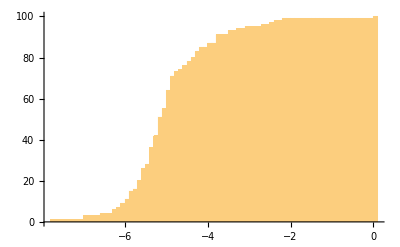

```mathematica
Histogram[Log[Abs[#]]&/@spec,{.1},"CumulativeCount"]
```

```mathematica
hlist=(specAbs=Sort[Log[Abs[#]]&/@spec];Join[{{specAbs_⟦1⟧-1,0}},Transpose[{specAbs,Table[n,{n,1,Length[specAbs]}]}],{{0.5,Length[specAbs]}}]);
```

```mathematica
StringJoin[Table["("<>ToString[N[hlist_⟦n,1⟧]]<>","<>ToString[hlist_⟦n,2⟧]<>")",{n,1,Length[hlist]}]]
```

(-8.79205,0)(-7.79205,1)(-6.96553,2)(-6.96553,3)(-6.5798,4)(-6.26998,5)(-6.26998,6)(-6.19925,7)(-6.05661,8)(-6.05661,9)(-5.95953,10)(-5.95953,11)(-5.87757,12)(-5.87757,13)(-5.87654,14)(-5.87654,15)(-5.75589,16)(-5.6916,17)(-5.6916,18)(-5.60808,19)(-5.60808,20)(-5.59782,21)(-5.59782,22)(-5.57483,23)(-5.57483,24)(-5.55731,25)(-5.55731,26)(-5.46811,27)(-5.44173,28)(-5.38656,29)(-5.38656,30)(-5.34592,31)(-5.34592,32)(-5.3278,33)(-5.3278,34)(-5.32357,35)(-5.32357,36)(-5.24979,37)(-5.24979,38)(-5.23231,39)(-5.23231,40)(-5.21199,41)(-5.21199,42)(-5.19541,43)(-5.19541,44)(-5.19235,45)(-5.19235,46)(-5.17803,47)(-5.17803,48)(-5.16164,49)(-5.16164,50)(-5.12838,51)(-5.07577,52)(-5.07577,53)(-5.05368,54)(-5.05368,55)(-4.99715,56)(-4.99715,57)(-4.92122,58)(-4.92122,59)(-4.91251,60)(-4.9078,61)(-4.9078,62)(-4.9061,63)(-4.9061,64)(-4.88772,65)(-4.88399,66)(-4.88399,67)(-4.87251,68)(-4.87251,69)(-4.83511,70)(-4.83511,71)(-4.7734,72)(-4.7734,73)(-4.62487,74)(-4.54086,75)(-4.54086,76)(-4.48619,77)(-4.48619,78)(-4.31897,79)(-4.31897,80)(-4.28883,81)(-4.28883,82)(-4.27214,83)(-4.10413,84)(-4.10413,85)(-3.99397,86)(-3.99397,87)(-3.77384,88)(-3.77384,89)(-3.71165,90)(-3.71165,91)(-3.44318,92)(-3.44318,93)(-3.21755,94)(-3.05285,95)(-2.66142,96)(-2.46435,97)(-2.32051,98)(-2.11289,99)(0.,100)(0.5,100)

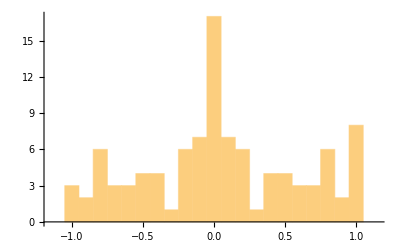

```mathematica
Histogram[Arg[#]/π&/@spec,{-1.15,1.15,.1}]
```

```mathematica
hlist=(specArg=Sort[Arg[#]/π&/@spec];Join[{{-1.15,0}},Transpose[{specArg,Table[n,{n,1,Length[specArg]}]}],{{1.5,Length[specArg]}}]);
```

```mathematica
StringJoin[Table["("<>ToString[N[hlist_⟦n,1⟧]]<>","<>ToString[hlist_⟦n,2⟧]<>")",{n,1,Length[hlist]}]]
```

(-1.15,0)(-0.988474,1)(-0.971284,2)(-0.966946,3)(-0.884629,4)(-0.8827,5)(-0.841441,6)(-0.83574,7)(-0.809663,8)(-0.78409,9)(-0.778485,10)(-0.774236,11)(-0.745139,12)(-0.737643,13)(-0.6818,14)(-0.647775,15)(-0.583273,16)(-0.550549,17)(-0.503946,18)(-0.474642,19)(-0.467919,20)(-0.463381,21)(-0.38788,22)(-0.382227,23)(-0.365685,24)(-0.353728,25)(-0.333885,26)(-0.222339,27)(-0.221336,28)(-0.181285,29)(-0.180649,30)(-0.179402,31)(-0.161911,32)(-0.130641,33)(-0.0943831,34)(-0.0877758,35)(-0.0875261,36)(-0.0737488,37)(-0.0549326,38)(-0.0531312,39)(-0.0308909,40)(-0.0147133,41)(0.,42)(0.,43)(0.,44)(0.,45)(0.,46)(0.,47)(0.,48)(0.,49)(0.,50)(0.,51)(0.,52)(0.,53)(0.,54)(0.0147133,55)(0.0308909,56)(0.0531312,57)(0.0549326,58)(0.0737488,59)(0.0875261,60)(0.0877758,61)(0.0943831,62)(0.130641,63)(0.161911,64)(0.179402,65)(0.180649,66)(0.181285,67)(0.221336,68)(0.222339,69)(0.333885,70)(0.353728,71)(0.365685,72)(0.382227,73)(0.38788,74)(0.463381,75)(0.467919,76)(0.474642,77)(0.503946,78)(0.550549,79)(0.583273,80)(0.647775,81)(0.6818,82)(0.737643,83)(0.745139,84)(0.774236,85)(0.778485,86)(0.78409,87)(0.809663,88)(0.83574,89)(0.841441,90)(0.8827,91)(0.884629,92)(0.966946,93)(0.971284,94)(0.988474,95)(1.,96)(1.,97)(1.,98)(1.,99)(1.,100)(1.5,100)

### Data for topic patterns

```mathematica
TopicClusters=DeleteCases[NonStopClusters,{_,_,_,"B",_,_,_,_}];
```

```mathematica
Length[TopicClusters]
```

202

```mathematica
SelectedClusters=TopicClusters;
```

```mathematica
TopicClustersSpanish=TopicClusters;
```

```mathematica
Timing[PesTopic=Table[Table[prepP=TransitionMeasure[SelectedClusters_⟦m,1⟧,SelectedClusters_⟦n,1⟧,SelectedClusters_⟦m,5⟧,SelectedClusters_⟦m,6⟧],{n,1,Length[SelectedClusters]}],{m,1,Length[SelectedClusters]}];]
```

{114.203,Null}

```mathematica
Timing[PesT=Table[v=Table[prepP=PesTopic_⟦m,n⟧;prepP_⟦1⟧*Exp[-prepP_⟦2⟧],{n,1,100}];v/Total[v],{m,1,100}];]
```

{0.046875,Null}

```mathematica
Timing[spec=Eigenvalues[PesT];]
```

{1.29688,Null}

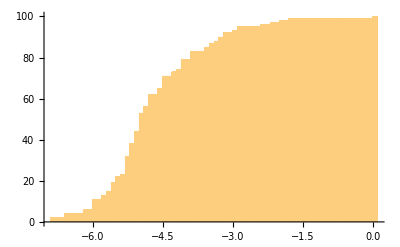

```mathematica
Histogram[Log[Abs[#]]&/@spec,{.1},"CumulativeCount"]
```

```mathematica
hlist=(specAbs=Sort[Log[Abs[#]]&/@spec];Join[{{specAbs_⟦1⟧-1,0}},Transpose[{specAbs,Table[n,{n,1,Length[specAbs]}]}],{{0.5,Length[specAbs]}}]);
```

```mathematica
StringJoin[Table["("<>ToString[N[hlist_⟦n,1⟧]]<>","<>ToString[hlist_⟦n,2⟧]<>")",{n,1,Length[hlist]}]]
```

(-7.8728,0)(-6.8728,1)(-6.8728,2)(-6.57594,3)(-6.57594,4)(-6.1339,5)(-6.1339,6)(-5.98754,7)(-5.98754,8)(-5.98012,9)(-5.96524,10)(-5.96524,11)(-5.72381,12)(-5.72381,13)(-5.63707,14)(-5.63707,15)(-5.54577,16)(-5.54577,17)(-5.52271,18)(-5.52271,19)(-5.43882,20)(-5.43882,21)(-5.41373,22)(-5.33955,23)(-5.27463,24)(-5.2718,25)(-5.2718,26)(-5.23459,27)(-5.23459,28)(-5.23349,29)(-5.23349,30)(-5.23013,31)(-5.23013,32)(-5.19928,33)(-5.19928,34)(-5.17709,35)(-5.17709,36)(-5.12615,37)(-5.12615,38)(-5.08204,39)(-5.08204,40)(-5.0797,41)(-5.0797,42)(-5.0009,43)(-5.0009,44)(-4.96568,45)(-4.96568,46)(-4.93799,47)(-4.93799,48)(-4.93664,49)(-4.93664,50)(-4.93539,51)(-4.90241,52)(-4.90241,53)(-4.85229,54)(-4.8324,55)(-4.8324,56)(-4.79784,57)(-4.79295,58)(-4.79295,59)(-4.7544,60)(-4.71508,61)(-4.71508,62)(-4.52721,63)(-4.526,64)(-4.526,65)(-4.49898,66)(-4.49898,67)(-4.48921,68)(-4.48921,69)(-4.45595,70)(-4.45595,71)(-4.2522,72)(-4.2522,73)(-4.15508,74)(-4.09458,75)(-4.09458,76)(-4.07474,77)(-4.01581,78)(-4.01581,79)(-3.88154,80)(-3.88154,81)(-3.8442,82)(-3.8442,83)(-3.53908,84)(-3.50801,85)(-3.48961,86)(-3.48961,87)(-3.33667,88)(-3.2402,89)(-3.2402,90)(-3.10809,91)(-3.10809,92)(-2.97792,93)(-2.86341,94)(-2.86341,95)(-2.30764,96)(-2.14582,97)(-1.99997,98)(-1.78704,99)(0.,100)(0.5,100)

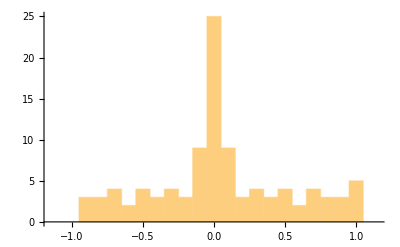

```mathematica
Histogram[Arg[#]/π&/@spec,{-1.15,1.15,.1}]
```

```mathematica
hlist=(specArg=Sort[Arg[#]/π&/@spec];Join[{{-1.15,0}},Transpose[{specArg,Table[n,{n,1,Length[specArg]}]}],{{1.5,Length[specArg]}}]);
```

```mathematica
StringJoin[Table["("<>ToString[N[hlist_⟦n,1⟧]]<>","<>ToString[hlist_⟦n,2⟧]<>")",{n,1,Length[hlist]}]]
```

(-1.15,0)(-0.91364,1)(-0.902871,2)(-0.852088,3)(-0.829578,4)(-0.804909,5)(-0.804679,6)(-0.734953,7)(-0.725509,8)(-0.705907,9)(-0.670591,10)(-0.628214,11)(-0.624485,12)(-0.545406,13)(-0.500497,14)(-0.499224,15)(-0.460474,16)(-0.444991,17)(-0.402858,18)(-0.382729,19)(-0.344361,20)(-0.322773,21)(-0.264445,22)(-0.26077,23)(-0.24984,24)(-0.23888,25)(-0.17088,26)(-0.145436,27)(-0.126334,28)(-0.10284,29)(-0.0971454,30)(-0.0929481,31)(-0.0858249,32)(-0.0813833,33)(-0.0648264,34)(-0.0620974,35)(-0.0290516,36)(-0.0276314,37)(-0.0250626,38)(-0.00804199,39)(-0.0043074,40)(0.,41)(0.,42)(0.,43)(0.,44)(0.,45)(0.,46)(0.,47)(0.,48)(0.,49)(0.,50)(0.,51)(0.,52)(0.,53)(0.,54)(0.,55)(0.0043074,56)(0.00804199,57)(0.0250626,58)(0.0276314,59)(0.0290516,60)(0.0620974,61)(0.0648264,62)(0.0813833,63)(0.0858249,64)(0.0929481,65)(0.0971454,66)(0.10284,67)(0.126334,68)(0.145436,69)(0.17088,70)(0.23888,71)(0.24984,72)(0.26077,73)(0.264445,74)(0.322773,75)(0.344361,76)(0.382729,77)(0.402858,78)(0.444991,79)(0.460474,80)(0.499224,81)(0.500497,82)(0.545406,83)(0.624485,84)(0.628214,85)(0.670591,86)(0.705907,87)(0.725509,88)(0.734953,89)(0.804679,90)(0.804909,91)(0.829578,92)(0.852088,93)(0.902871,94)(0.91364,95)(1.,96)(1.,97)(1.,98)(1.,99)(1.,100)(1.5,100)

### Word translation

#### Bulk vectors

```mathematica
EnglishRef=TopicClustersEnglish;
```

```mathematica
SpanishRef=TopicClustersSpanish;
```

```mathematica
PandPChapEnglish=StringSplit[ExampleData[{"Text","PrideAndPrejudice"}],"Chapter "~~DigitCharacter..~~" "];
```

```mathematica
Length[PandPChapEnglish]
```

61

```mathematica
VecEnglish=Table[{EnglishRef_⟦k,1⟧,StringCount[PandPChapEnglish,WordBoundary~~Alternatives@@(#_⟦1⟧&/@EnglishRef_⟦k,1⟧)~~WordBoundary,IgnoreCase->True]},{k,1,Length[EnglishRef]}];
```

```mathematica
PandPChapSpanish=StringSplit[StringReplace[ImportString[StringReplace[Import["Orgullo y prejuicio (Rodriguez).txt"],{"\n":>"垚"," ?":>"?"," !":>"!"," :":>":"," ;":>";","« ":>"«"," »":>"»","¬":>""}],"HTML"],"垚":>"\n\n"],DigitCharacter..~~"\n"];
```

```mathematica
Length[PandPChapSpanish]
```

61

```mathematica
VecSpanish=Table[{SpanishRef_⟦k,1⟧,StringCount[PandPChapSpanish,WordBoundary~~Alternatives@@(#_⟦1⟧&/@SpanishRef_⟦k,1⟧)~~WordBoundary,IgnoreCase->True]},{k,1,Length[SpanishRef]}];
```

```mathematica
FlatScreenedPairs=Flatten[Table[{#_⟦1⟧,#_⟦2,k⟧},{k,1,Length[#_⟦2⟧]}]&/@Select[Table[{EnglishRef[[k,1]],#_⟦1⟧&/@Select[VecSpanish,JaccardRuzickaSim[#_⟦2⟧,Cases[VecEnglish,{EnglishRef[[k,1]],___}]_⟦1,2⟧]≥Max[1-7/100*√61,1-√(Length[Select[Min[#]&/@Transpose[{#_⟦2⟧,Cases[VecEnglish,{EnglishRef[[k,1]],___}]_⟦1,2⟧}],#>0&]]/Total[Max[#]&/@Transpose[{#_⟦2⟧,Cases[VecEnglish,{EnglishRef[[k,1]],___}]_⟦1,2⟧}]])]&]},{k,1,Length[EnglishRef]}],Length[#_⟦2⟧]>0&],1];
```

```mathematica
SiftedTags=Union[(#_⟦1⟧&/@FlatScreenedPairs)];SiftedEnglishRef=Reverse[SortBy[Table[Cases[EnglishRef,{SiftedTags[[k]],___}]_⟦1⟧,{k,1,Length[SiftedTags]}],#_⟦3⟧&]];
```

```mathematica
SiftedTags=Union[(#_⟦2⟧&/@FlatScreenedPairs)];SiftedSpanishRef=Reverse[SortBy[Table[Cases[SpanishRef,{SiftedTags[[k]],___}]_⟦1⟧,{k,1,Length[SiftedTags]}],#_⟦3⟧&]];
```

```mathematica
Length[SiftedEnglishRef]
```

92

```mathematica
Length[SiftedSpanishRef]
```

92

#### Spectral parameters for English

```mathematica
FromTopics=SiftedEnglishRef;
```

```mathematica
FromDelta=ReadDelta[#]&/@FromTopics;
```

```mathematica
FromN=(#_⟦3⟧-1)&/@FromTopics;
```

```mathematica
AbsoluteTiming[KinSpecSWLongTag[TopicClustersEnglish,PenTopic,#_⟦1⟧&/@FromTopics];]
```

{47.2512,Null}

```mathematica
FromKinQ=KinQ;
```

```mathematica
FromEta=SemanticComplexities;
```

#### Spectral parameters for Spanish

```mathematica
ToTopicsSpanish=SiftedSpanishRef;
```

```mathematica
Length[ToTopicsSpanish]
```

92

```mathematica
ToDeltaSpanish=ReadDelta[#]&/@ToTopicsSpanish;
```

```mathematica
ToNSpanish=(#_⟦3⟧-1)&/@ToTopicsSpanish;
```

```mathematica
AbsoluteTiming[KinSpecSWLongTag[TopicClustersSpanish,PesTopic,#_⟦1⟧&/@ToTopicsSpanish];]
```

{47.4549,Null}

```mathematica
ToKinSpanish=KinQ;
```

```mathematica
ToEtaSpanish=SemanticComplexities;
```

#### Translation

```mathematica
AbsoluteTiming[fromLabeled=Transpose[{#_⟦1⟧&/@FromTopics,FromKinQ}];toLabeled=Transpose[{#_⟦1⟧&/@ToTopicsSpanish,ToKinSpanish}];Report=Table[{FlatScreenedPairs_⟦k⟧,(JaccardRuzickaSim[Cases[fromLabeled,{FlatScreenedPairs_⟦k,1⟧,_}]_⟦1,2⟧,Cases[toLabeled,{FlatScreenedPairs_⟦k,2⟧,_}]_⟦1,2⟧])},{k,1,Length[FlatScreenedPairs]}];]
```

{0.0137983,Null}

```mathematica
prep=Union[Select[Table[{Report_⟦n,1,1⟧,Report_⟦n,1,2⟧,Report_⟦n,2⟧},{n,1,Length[Report]}],#_⟦3⟧≥0.7&]];g=Graph[(#_⟦1⟧->#_⟦2⟧)&/@prep,EdgeWeight->(#_⟦3⟧&/@prep)];(KuhnSln={#,FindRowRank[#,prep],FindColRank[#,prep]}&/@Select[{#,PropertyValue[{g,#},EdgeWeight]}&/@FindIndependentEdgeSet[g],#_⟦2⟧>0&])//TableForm
```

{{Brighton,24}}->{{brighton,24}}
0.90209879437826 | 1 | 1
{{de,39}}->{{bourgh,39}}
0.91175317358466 | 1 | 1
{{five,30}}->{{cinco,30},{cincuenta,5}}
0.92295056846319 | 1 | 1
{{library,23}}->{{biblioteca,24}}
0.93372730208132 | 1 | 1
{{London,55}}->{{londres,56}}
0.77299035511716 | 1 | 1
{{Meryton,57}}->{{meryton,56}}
0.90863359251372 | 1 | 1
{{money,26}}->{{dinero,26}}
0.87550191032881 | 1 | 1
{{Mrs,343}}->{{mrs,354},{señora,26},{señoras,15}}
0.8381259981935 | 1 | 1
{{Netherfield,73}}->{{netherfield,72}}
0.80185828466601 | 1 | 1
{{oh,95}}->{{oh,60}}
0.74853722088676 | 1 | 1
{{park,22}}->{{park,5},{parque,17}}
0.83484159446942 | 1 | 1
{{Pemberley,53}}->{{pemberley,53}}
0.91013520989497 | 1 | 1
{{thousand,34}}->{{mil,32}}
0.84389786255802 | 1 | 1
{{Rosings,49}}->{{rosings,49}}
0.90863045075038 | 1 | 1
{{sir,78}}->{{sir,47}}
0.83484421188919 | 2 | 2
{{William,40},{William's,6}}->{{william,48}}
0.87793254846633 | 1 | 1
{{town,64}}->{{capitán,4},{capital,48}}
0.88955439895692 | 1 | 1
{{Catherine,110},{Catherine's,16}}->{{catherine,118}}
0.88109893876889 | 1 | 1
{{Charlotte,68},{Charlotte's,17}}->{{charlotte,89}}
0.95569705305756 | 1 | 1
{{civilities,7},{civility,42}}->{{cortés,12},{cortesano,1},{corteses,4},{cortesía,45},{cortesías,3}}
0.91062414958348 | 1 | 1
{{Collins,156},{Collins's,24}}->{{collins,190}}
0.89039434654483 | 1 | 1
{{colonel,65},{colonel's,1}}->{{coronada,1},{coronel,68}}
0.78820026398291 | 1 | 1
{{Darcy,374},{Darcy's,44}}->{{darcy,479}}
0.90940689094903 | 1 | 1
{{door,32},{doors,8}}->{{puerta,33},{puertas,2}}
0.93586442530879 | 1 | 1
{{father,116},{father's,19}}->{{padre,119},{papá,21},{padres,10}}
0.89462619531107 | 1 | 1
{{Fitzwilliam,32},{Fitzwilliam's,5}}->{{fitzwilliam,37}}
0.92461841818338 | 1 | 1
{{four,33},{four-and-twenty,1}}->{{cuatro,30},{cuatrocientas,1}}
0.87520787919306 | 1 | 1
{{girl,38},{girls,45}}->{{muchísimas,1},{muchísimo,6},{muchacha,40},{muchachas,41},{muchacho,11},{muchachos,2}}
0.81778467994343 | 1 | 1
{{ignorance,7},{ignorant,16}}->{{ignora,2},{ignorante,3},{ignorarlo,2},{ignorarlos,1},{ignoraba,6},{ignoraban,2},{ignorantes,2},{ignorar,1},{ignoraría,1},{ignoras,1},{ignore,1},{ignoro,9}}
0.81169140563794 | 1 | 1
{{Jane,263},{Jane's,28}}->{{jane,327}}
0.89875414180216 | 1 | 1
{{Kitty,69},{Kitty's,2}}->{{kitty,74}}
0.91623662524661 | 1 | 1
{{Lydia,133},{Lydia's,38}}->{{lydia,174}}
0.93144614629858 | 1 | 1
{{Mary,38},{Mary's,1}}->{{mary,57}}
0.71009648436401 | 1 | 1
{{poor,38},{poorly,3}}->{{pobre,27},{pobres,5},{pobreza,2}}
0.82273212964562 | 1 | 1
{{regiment,19},{regiment's,3}}->{{regimiento,30}}
0.85007225372988 | 1 | 1
{{surprise,37},{surprised,35}}->{{sorprende,2},{sorprendente,4},{sorprenderle,1},{sorprenden,1},{sorprenderán,1},{sorprendería,1},{sorprendes,1},{sorprendía,2},{sorprendida,14},{sorprendidas,4},{sorprendidos,3},{sorprendido,11},{sorprendió,10},{sorprendiera,1},{sorprendieron,1}}
0.88249580197739 | 1 | 1
{{ten,33},{tens,1}}->{{diez,31}}
0.88218879765403 | 1 | 1
{{week,29},{weeks,18}}->{{semana,27},{semanas,21}}
0.8685279113698 | 1 | 1
{{Wickham,162},{Wickham's,32}}->{{wickham,214}}
0.85974567374165 | 1 | 1
{{window,16},{windows,6}}->{{ventana,14},{ventanas,8},{ventanilla,1},{ventanillas,1}}
0.83467098925803 | 1 | 1
{{ask,32},{asked,40},{asking,14}}->{{pregunta,17},{preguntarle,12},{preguntarte,2},{pregunto,1},{preguntó,44}}
0.84336412360895 | 1 | 1
{{aunt,78},{aunt's,6},{aunts,1}}->{{tía,62},{tías,1}}
0.89054124164853 | 1 | 1
{{beautiful,15},{beauties,4},{beauty,27}}->{{hermosa,13},{hermosamente,1},{hermosas,6},{hermosísimo,1},{hermoso,5},{hermosos,4},{hermosura,4}}
0.85745730794088 | 1 | 1
{{Bennet,294},{Bennet's,29},{Bennets,10}}->{{bennet,317}}
0.90117228953785 | 1 | 1
{{cried,91},{cry,1},{crying,2}}->{{exclamaba,3},{exclamaban,1},{exclamando,2},{exclamar,3},{exclamación,2},{exclamaciones,4},{exclamó,89}}
0.88494044202121 | 1 | 1
{{Eliza,22},{Elizabeth,597},{Elizabeth's,38}}->{{lizzy,826}}
0.70919531278751 | 1 | 1
{{evening,72},{evening's,2},{evenings,4}}->{{velada,39},{veladas,10},{velara,1},{veloz,1},{velozmente,1},{vil,1}}
0.78720665367443 | 1 | 1
{{eye,15},{eyeing,1},{eyes,52}}->{{ojeada,1},{ojos,44}}
0.73807619820981 | 1 | 1
{{Forster,38},{Forster's,1},{Forsters,1}}->{{forster,39}}
0.92825496729222 | 1 | 1
{{Gardiner,84},{Gardiner's,13},{Gardiners,6}}->{{gardiner,107}}
0.90451426951224 | 1 | 1
{{Hurst,32},{Hurst's,1},{Hursts,1}}->{{hurst,35}}
0.76720444923913 | 1 | 1
{{husband,42},{husband's,8},{husbands,4}}->{{maridos,1},{marido,55}}
0.87627629617163 | 1 | 1
{{letter,115},{letters,16},{letter-paper,1}}->{{carta,118},{cartas,22}}
0.84861470905467 | 1 | 1
{{man,145},{man's,5},{men,33}}->{{hombros,1},{hombre,82},{hombres,23},{hombro,1}}
0.89103714815158 | 1 | 1
{{maternal,2},{mother,110},{mother's,25}}->{{madre,115},{mamá,25}}
0.91464414962806 | 1 | 1
{{niece,20},{niece's,2},{nieces,9}}->{{sobrina,22},{sobrinas,10},{sobrino,25}}
0.8548583993401 | 1 | 1
{{Phillip's,1},{Phillips,26},{Phillips's,5}}->{{philips,34}}
0.90648439002371 | 1 | 1
{{read,40},{reading,14},{reader,3}}->{{lea,1},{lee,1},{leerla,3},{leerlo,1},{leerte,2},{leemos,1},{leer,14},{leérsela,1},{leía,5},{leída,1},{leído,7},{leyendo,6},{leyera,2},{leyes,2},{leyese,1},{leyó,11}}
0.84791108018354 | 1 | 1
{{uncle,59},{uncle's,9},{uncles,3}}->{{tío,47},{tíos,26}}
0.92932224352184 | 1 | 1
{{year,28},{years,33},{years',2}}->{{año,22},{años,53}}
0.84548033687508 | 1 | 1
{{young,130},{younger,30},{youngest,13}}->{{joven,65},{jóvenes,34}}
0.84528604439918 | 1 | 1
{{best,41},{better,92},{good,184},{good-humoured,6}}->{{buen,48},{buena,47},{buenas,22},{bonita,9},{bonitas,4},{bonito,4},{bonitos,2},{bueno,15},{mejor,116},{mejores,8},{mejora,3},{mejorarlas,1},{mejorarlo,1},{mejorado,7},{mejorando,1},{mejorar,1},{mejoras,1},{mejoría,2},{mejoró,1}}
0.71141102866438 | 1 | 1
{{Bingley,257},{Bingley's,49},{Bingleys,4},{Bingleys',1}}->{{bingley,339}}
0.84928636980977 | 1 | 1
{{brother,62},{brotherly,2},{brother's,13},{brothers,2}}->{{hermano,62},{hermanos,5}}
0.84997570780608 | 1 | 1
{{complied,4},{compliment,26},{compliments,11},{compliance,1}}->{{cumpla,1},{cumplidos,13},{cumplido,17},{cumplimentó,2},{cumplimiento,2},{cumplió,2},{cumplir,9},{cumpliré,1},{cumpliese,1}}
0.75491600325109 | 1 | 1
{{daily,3},{day,130},{day's,4},{days,30}}->{{día,120},{diario,3},{días,60}}
0.87652021620414 | 1 | 1
{{daughter,78},{daughter's,7},{daughters,49},{daughters',1}}->{{hija,97},{hijas,81}}
0.93891005107605 | 1 | 1
{{dine,16},{dined,8},{dines,1},{dining,6}}->{{coman,1},{comemos,1},{comen,1},{comer,40},{comería,1},{comía,1},{comió,3},{comida,15},{comidas,1},{comido,7},{comiste,1},{comodidad,3},{cómodas,1},{cómodo,3},{comadres,1}}
0.77160917171418 | 1 | 1
{{fortune,39},{fortunes,1},{fortunate,15},{fortunately,2}}->{{fortuna,39}}
0.90417955708663 | 1 | 1
{{honour,42},{honoured,9},{honours,2},{honourable,6}}->{{honor,33},{honorable,3},{honorables,1}}
0.91022021615807 | 1 | 1
{{look,57},{looked,74},{looking,29},{looks,12}}->{{mira,8},{mirarla,2},{mirarlo,3},{mirarnos,1},{miraba,15},{miraban,2},{mirabas,1},{mirad,1},{mirada,24},{miradas,11},{mirado,2},{mirando,8},{mirándolo,1},{mirar,10},{mirara,1},{miraron,4},{miro,1},{miró,34}}
0.86531440398976 | 1 | 1
{{Lucas,65},{Lucas's,5},{Lucases,13},{Lucases',1}}->{{lucas,80}}
0.86393854980475 | 1 | 1
{{promise,17},{promised,21},{promises,3},{promising,4}}->{{promete,3},{prometerlo,1},{prometerte,1},{prométeme,1},{prometer,2},{prometérselo,1},{prometí,1},{prometía,3},{prometían,1},{prometida,4},{prometido,10},{prometiendo,1},{prometiéndome,1},{prometió,9},{prometedora,2}}
0.93264338471544 | 1 | 1
{{send,24},{sending,1},{sends,1},{sent,20}}->{{envía,2},{enviarlas,2},{enviarle,1},{enviarte,1},{enviada,3},{enviado,8},{enviar,6},{enviará,1},{enviaré,1},{envías,1},{enviase,3},{enviaste,1},{envíe,2},{envió,7},{envío,2}}
0.85985862067849 | 1 | 1
{{vanish,1},{vanished,2},{vain,20},{vanity,18}}->{{vanidad,18},{vana,2},{vanamente,1},{vanas,2},{vano,14}}
0.82540414182853 | 1 | 1
{{carriage,44},{carriages,6},{carried,8},{carry,5},{carrying,4}}->{{coche,50},{cochero,3},{coches,3}}
0.86035589274762 | 1 | 1
{{console,9},{consoled,2},{consoling,3},{consolation,10},{consolatory,1}}->{{consolarla,3},{consolarte,1},{consuela,2},{consolaba,2},{consolada,1},{consuelan,1},{consolándose,1},{consolar,2},{consolara,1},{consolase,1},{consueles,1},{consuelo,21},{consuelos,1},{consolador,1},{consoladora,2}}
0.801268256695 | 1 | 1
{{happily,5},{happiness,72},{happy,83},{happier,3},{happiest,10}}->{{felicidad,58},{feliz,56},{felices,5},{felicitarlas,1},{felicitarme,1},{felicito,2},{felicitó,2},{felizmente,6},{felicitado,1},{felicitando,3},{felicitándola,2},{felicitándose,1},{felicitaran,2},{felicitaría,1},{felicitación,4},{felicitaciones,2},{felicite,1}}
0.74303695932744 | 1 | 1
{{invite,6},{invited,11},{inviting,3},{invitation,34},{invitations,1}}->{{invitarlas,1},{invitarlo,4},{invitarlos,2},{invitaba,1},{invitada,3},{invitados,9},{invitado,6},{invitándola,1},{invitándolas,1},{invitándote,1},{invitar,2},{invitara,1},{invitará,1},{invitarían,1},{invitaron,3},{invitas,1},{invitase,2},{invitasen,1},{invitación,30},{invitaciones,5},{invite,1},{invitó,16},{invítalo,1}}
0.86246584988499 | 1 | 1
{{miss,283},{missed,3},{missing,1},{missent,2},{missish,1}}->{{miss,211},{señorita,14},{señoritas,6}}
0.7610817880525 | 1 | 1
{{pride,47},{prided,1},{proud,22},{proudly,1},{proudest,1}}->{{orgullo,37},{orgullosa,5},{orgulloso,16}}
0.88007304018098 | 1 | 1
{{refuse,9},{refused,6},{refusing,7},{refusal,7},{refusals,1}}->{{rechaza,2},{rechazarla,2},{rechazarle,1},{rechazarlo,3},{rechazarme,3},{rechazaba,2},{rechazada,1},{rechazados,2},{rechazado,8},{rechazando,1},{rechazar,9},{rechazaron,1},{rechaces,1},{rechazo,6},{rechazó,3}}
0.86655561075188 | 1 | 1
{{serve,2},{serving,1},{servant,15},{servant's,2},{servants,12}}->{{criada,4},{criadas,3},{criados,11},{criado,13}}
0.83921401224443 | 1 | 1
{{woman,55},{womanly,1},{woman's,4},{women,19},{women's,1}}->{{mujer,86},{mujeres,32}}
0.81441228236363 | 1 | 1
{{deceitful,2},{deceive,4},{deceived,13},{deceives,1},{deceiving,2},{deception,1}}->{{engaña,2},{engañarla,1},{engañarlo,1},{engañarme,1},{engañarse,1},{engañaban,1},{engañada,3},{engañados,3},{engañado,3},{engañar,2},{engañará,1},{engañarás,1},{engañe,1},{engaño,3},{engañó,1},{engañoso,2}}
0.77443712143228 | 1 | 1
{{office,6},{officer,8},{officers,29},{officers',2},{officiousness,1},{officious,3}}->{{oficial,7},{oficiales,32}}
0.90485306977888 | 1 | 1
{{write,39},{writes,1},{writing,12},{written,19},{writer,3},{wrote,21}}->{{escriba,4},{escribas,1},{escribe,5},{escríbeme,1},{escribí,3},{escribirlas,1},{escribirle,1},{escribirme,2},{escribirte,1},{escribía,1},{escribiendo,4},{escribiéndole,1},{escribió,9},{escribir,31},{escribiera,1},{escribirás,1},{escribiré,2},{escribiese,1},{escribo,2}}
0.89288525979403 | 1 | 1
{{respect,30},{respected,3},{respectful,1},{respecting,3},{respects,6},{respectability,5},{respectable,13},{respectable-looking,1}}->{{respetaba,1},{respetabilidad,5},{respetable,11},{respetables,2},{respetadas,1},{respetado,1},{respetar,1},{respeto,12},{respetos,7},{respetuosa,1},{respetuoso,1},{respetuosos,1}}
0.82392567618921 | 1 | 1
{{gentle,5},{gentleness,4},{gentlemen,34},{gentlemen's,3},{gentleman,32},{gentleman's,8},{gentlemanlike,8},{gentlest,1},{gentlewoman,1}}->{{caballeros,35},{caballerizas,1},{caballero,44},{caballerosamente,2},{caballeroso,3},{caballo,6},{caballos,10}}
0.83378708112947 | 1 | 1

```mathematica
ResiftedTags=Union[(#_⟦1⟧&/@prep)];ResiftedEnglishRef=Reverse[SortBy[Table[Cases[EnglishRef,{ResiftedTags[[k]],___}]_⟦1⟧,{k,1,Length[ResiftedTags]}],#_⟦3⟧&]];
```

```mathematica
ResiftedTags=Union[(#_⟦2⟧&/@prep)];ResiftedSpanishRef=Reverse[SortBy[Table[Cases[SpanishRef,{ResiftedTags[[k]],___}]_⟦1⟧,{k,1,Length[ResiftedTags]}],#_⟦3⟧&]];
```

```mathematica
SemanticSim={Position[ResiftedEnglishRef,{#_⟦1⟧,___}]_⟦1,1⟧,Position[ResiftedSpanishRef,{#_⟦2⟧,___}]_⟦1,1⟧,#_⟦3⟧}&/@prep;
```

```mathematica
OptimalNodes={Position[ResiftedEnglishRef,{#_⟦1,1,1⟧,___}]_⟦1,1⟧,Position[ResiftedSpanishRef,{#_⟦1,1,2⟧,___}]_⟦1,1⟧,#_⟦2,1,1⟧,#_⟦3,1,1⟧}&/@KuhnSln;
```

```mathematica
Export["PnP_EnglishSpanish.txt","%tournament\n"<>StringJoin[Riffle[Flatten["\\put("<>ToString[1.5+1+4#_⟦2⟧]<>","<>ToString[90-4#_⟦1⟧]<>"){\\color[rgb]"<>ToString[TempRGB[#_⟦3⟧]]<>"{\\rule{4pt}{4pt}}}"&/@SemanticSim],"\n"]]<>"\n%crosshairs\n"<>StringJoin[Riffle["\n%"<>ResiftedEnglishRef[[#_⟦1⟧,1,1,1]]<>"_"<>ResiftedSpanishRef[[#_⟦2⟧,1,1,1]]<>"
\\put("<>ToString[1.5+4#_⟦2⟧+3]<>","<>ToString[90-4#_⟦1⟧+2]<>"){\\color{green}\\linethickness{"<>ToString[1.5/#_⟦3⟧]<>"pt}\\line(-1,0){"<>ToString[4#_⟦2⟧-2]<>"}\\linethickness{"<>ToString[1.5/#_⟦4⟧]<>"pt}\\line(0,1){"<>ToString[4#_⟦1⟧-2]<>"}}"&/@OptimalNodes,"\n"]]];
```

#### English labels

```mathematica
FromClusters=ResiftedEnglishRef;
```

```mathematica
ScoredCluster={#_⟦1⟧,#_⟦2⟧,#_⟦3⟧,Total[#_⟦3⟧],#_⟦5⟧}&/@((prep=Transpose[CensorCluster[#_⟦1⟧]];{#_⟦2⟧,prep_⟦1⟧,prep_⟦2⟧,#_⟦3⟧,#_⟦4⟧})&/@FromClusters);
```

```mathematica
EnglishCompress[w_]:=StringReplace[w,{"ai":>"𝔸","ea":>"𝕀","ou":>"𝕌","ee":>"𝔼","oo":>"𝕆"}]
```

```mathematica
EnglishDecompress[w_]:=StringReplace[w,{"𝔸":>"ai","𝕀":>"ea","𝕌":>"ou","𝔼":>"ee","𝕆":>"oo"}]
```

```mathematica
EvenOut[cl_]:=(prep=EnglishCompress[cl_⟦1⟧];L=Max[StringLength[prep]];{#_⟦1⟧<>StringJoin[Table[" ",{L-StringLength[#_⟦1⟧]}]],#_⟦2⟧}&/@Transpose[{prep,cl_⟦2⟧}])
```

```mathematica
SplitEven[ecl_]:=(L=StringLength[ecl_⟦1,1⟧];Table[{m,EnglishDecompress[StringTake[#_⟦1⟧,{m}]],#_⟦2⟧}&/@ecl,{m,1,L}]);
```

```mathematica
MergeStem[spl_]:=SortBy[(prep=ConnectedComponents[Graph[Join[Table[If[(Length[Union[#_⟦2⟧&/@spl_⟦n⟧]]==1)&&(Length[Union[#_⟦2⟧&/@spl_⟦n+1⟧]]==1),spl_⟦n⟧<->spl_⟦n+1⟧,spl_⟦n⟧<->spl_⟦n⟧],{n,1,Length[spl]-1}],{Last[spl]<->Last[spl]}]]];If[Length[#]>1,{{SortBy[Transpose[#]_⟦1⟧,First]_⟦1,1⟧,StringJoin[#1_⟦2⟧&/@SortBy[Transpose[#]_⟦1⟧,First]],Total[#1_⟦3⟧&/@#_⟦1⟧]}},Flatten[#,1]]&/@prep),First]
```

```mathematica
ColSort[col_]:={#_⟦1⟧,#_⟦2⟧,#_⟦3⟧}&/@Reverse[SortBy[{Flatten[Union[#_⟦1⟧]],Union[#_⟦2⟧]_⟦1⟧,Total[#_⟦3⟧],Min[#_⟦4⟧]}&/@(Transpose[#]&/@(ConnectedComponents[Graph[Join[Table[If[col_⟦k,2⟧==col_⟦k+1,2⟧,{col_⟦k,1⟧,col_⟦k,2⟧,col_⟦k,3⟧,k}<->{col_⟦k+1,1⟧,col_⟦k+1,2⟧,col_⟦k+1,3⟧,k+1},{col_⟦k,1⟧,col_⟦k,2⟧,col_⟦k,3⟧,k}<->{col_⟦k,1⟧,col_⟦k,2⟧,col_⟦k,3⟧,k}],{k,1,Length[col]-1}],{{col_⟦Length[col],1⟧,col_⟦Length[col],2⟧,col_⟦Length[col],3⟧,Length[col]}<->{col_⟦Length[col],1⟧,col_⟦Length[col],2⟧,col_⟦Length[col],3⟧,Length[col]}}]]])),Last]]
```

```mathematica
CumHeight[cl_]:=(ch=0;s={};For[n=1,n<=Length[cl],n++,{s=Join[s,{{cl_⟦n,1⟧,cl_⟦n,2⟧,cl_⟦n,3⟧,ch}}];ch=ch+cl_⟦n,3⟧}];s)
```

```mathematica
Word2BarChart[cl_]:=CumHeight[#]&/@(ColSort[#]&/@MergeStem[SplitEven[EvenOut[cl]]])
```

```mathematica
Export["EnglishLabels_for_Spanish_PnP.txt",StringJoin[Table[(BCData=Word2BarChart[{ScoredCluster_⟦k,2⟧,ScoredCluster_⟦k,3⟧}];H=ScoredCluster_⟦k,4⟧;"\\put("<>ToString[5-3Total[Max/@StringLength/@(Transpose[#]_⟦2⟧&/@BCData)]]<>","<>ToString[91.75-1.5-4k]<>"){"<>"\\textbf{"<>"\\setlength{\\unitlength}{3pt}"<>StringJoin[hpos=0;Table[hinc=Max[StringLength/@Transpose[BCData_⟦m⟧]_⟦2⟧];hpos=hpos+hinc;Table[If[BCData_⟦m,n,2⟧==" ","","\\BC{"<>ToString[hpos-hinc]<>"}{"<>ToString[N[Round[BCData_⟦m,n,4⟧/H,10^-3]]]<>"}{"<>(ToString[hinc])<>"}{"<>ToString[N[Round[BCData_⟦m,n,3⟧/H,10^-3]]]<>"}{"<>ToUpperCase[BCData_⟦m,n,2⟧]<>"}\n"],{n,1,Length[BCData_⟦m⟧]}],{m,1,Length[BCData]}]])<>"}}\n",{k,1,Length[ScoredCluster]}]]];
```

#### Spanish labels

```mathematica
FromClusters=ResiftedSpanishRef;
```

```mathematica
ScoredCluster={#_⟦1⟧,#_⟦2⟧,#_⟦3⟧,Total[#_⟦3⟧],#_⟦5⟧}&/@((prep=Transpose[CensorCluster[#_⟦1⟧]];{#_⟦2⟧,prep_⟦1⟧,prep_⟦2⟧,#_⟦3⟧,#_⟦4⟧})&/@FromClusters);
```

```mathematica
SpanishCompress[w_]:=StringReplace[w,{"ie":>"𝕀","üe":>"𝕌","ié":>"𝔼",(h:Except["q"|"g"])~~"ue":>h<>"𝕆","zc":>"ℂ","zg":>"𝔾","sg":>"𝕊"}]
```

```mathematica
SpanishDecompress[w_]:=StringReplace[w,{"𝕀":>"ie","𝕌":>"üe","𝔼":>"ié","𝕆":>"ue","ℂ":>"zc","𝔾":>"zg","𝕊":>"sg"}]
```

```mathematica
ClusterCount={{"avergonzasteis","avergonzó","avergüence"},{10,72,83}}
```

{{avergonzasteis,avergonzó,avergüence},{10,72,83}}

```mathematica
EvenOut[cl_]:=(prep=SpanishCompress[cl_⟦1⟧];L=Max[StringLength[prep]];{#_⟦1⟧<>StringJoin[Table[" ",{L-StringLength[#_⟦1⟧]}]],#_⟦2⟧}&/@Transpose[{prep,cl_⟦2⟧}])
```

```mathematica
EvenOut[ClusterCount]
```

{{avergonzasteis,10},{avergonzó     ,72},{averg𝕌nce     ,83}}

```mathematica
SplitEven[ecl_]:=(L=StringLength[ecl_⟦1,1⟧];Table[{m,SpanishDecompress[StringTake[#_⟦1⟧,{m}]],#_⟦2⟧}&/@ecl,{m,1,L}]);
```

```mathematica
SplitEven[EvenOut[ClusterCount]]//Transpose//TableForm
```

1
a
10 | 2
v
10 | 3
e
10 | 4
r
10 | 5
g
10 | 6
o
10 | 7
n
10 | 8
z
10 | 9
a
10 | 10
s
10 | 11
t
10 | 12
e
10 | 13
i
10 | 14
s
10
1
a
72 | 2
v
72 | 3
e
72 | 4
r
72 | 5
g
72 | 6
o
72 | 7
n
72 | 8
z
72 | 9
ó
72 | 10
 
72 | 11
 
72 | 12
 
72 | 13
 
72 | 14
 
72
1
a
83 | 2
v
83 | 3
e
83 | 4
r
83 | 5
g
83 | 6
üe
83 | 7
n
83 | 8
c
83 | 9
e
83 | 10
 
83 | 11
 
83 | 12
 
83 | 13
 
83 | 14
 
83

```mathematica
Last[SplitEven[EvenOut[ClusterCount]]]
```

{{14,s,10},{14, ,72},{14, ,83}}

```mathematica
MergeStem[spl_]:=SortBy[(prep=ConnectedComponents[Graph[Join[Table[If[(Length[Union[#_⟦2⟧&/@spl_⟦n⟧]]==1)&&(Length[Union[#_⟦2⟧&/@spl_⟦n+1⟧]]==1),spl_⟦n⟧<->spl_⟦n+1⟧,spl_⟦n⟧<->spl_⟦n⟧],{n,1,Length[spl]-1}],{Last[spl]<->Last[spl]}]]];If[Length[#]>1,{{SortBy[Transpose[#]_⟦1⟧,First]_⟦1,1⟧,StringJoin[#1_⟦2⟧&/@SortBy[Transpose[#]_⟦1⟧,First]],Total[#1_⟦3⟧&/@#_⟦1⟧]}},Flatten[#,1]]&/@prep),First]
```

```mathematica
MergeStem[SplitEven[EvenOut[ClusterCount]]]//TableForm
```

1
averg
165 |  | 
6
o
10 | 6
o
72 | 6
üe
83
7
n
10 | 7
n
72 | 7
n
83
8
z
10 | 8
z
72 | 8
c
83
9
a
10 | 9
ó
72 | 9
e
83
10
s
10 | 10
 
72 | 10
 
83
11
t
10 | 11
 
72 | 11
 
83
12
e
10 | 12
 
72 | 12
 
83
13
i
10 | 13
 
72 | 13
 
83
14
s
10 | 14
 
72 | 14
 
83

```mathematica
ColSort[col_]:={#_⟦1⟧,#_⟦2⟧,#_⟦3⟧}&/@Reverse[SortBy[{Flatten[Union[#_⟦1⟧]],Union[#_⟦2⟧]_⟦1⟧,Total[#_⟦3⟧],Min[#_⟦4⟧]}&/@(Transpose[#]&/@(ConnectedComponents[Graph[Join[Table[If[col_⟦k,2⟧==col_⟦k+1,2⟧,{col_⟦k,1⟧,col_⟦k,2⟧,col_⟦k,3⟧,k}<->{col_⟦k+1,1⟧,col_⟦k+1,2⟧,col_⟦k+1,3⟧,k+1},{col_⟦k,1⟧,col_⟦k,2⟧,col_⟦k,3⟧,k}<->{col_⟦k,1⟧,col_⟦k,2⟧,col_⟦k,3⟧,k}],{k,1,Length[col]-1}],{{col_⟦Length[col],1⟧,col_⟦Length[col],2⟧,col_⟦Length[col],3⟧,Length[col]}<->{col_⟦Length[col],1⟧,col_⟦Length[col],2⟧,col_⟦Length[col],3⟧,Length[col]}}]]])),Last]]
```

```mathematica
ColSort[#]&/@MergeStem[SplitEven[EvenOut[ClusterCount]]]//TableForm
```

1
averg
165 |  | 
6
üe
83 | 6
o
82 | 
7
n
165 |  | 
8
c
83 | 8
z
82 | 
9
e
83 | 9
ó
72 | 9
a
10
10
 
155 | 10
s
10 | 
11
 
155 | 11
t
10 | 
12
 
155 | 12
e
10 | 
13
 
155 | 13
i
10 | 
14
 
155 | 14
s
10 |

```mathematica
CumHeight[cl_]:=(ch=0;s={};For[n=1,n<=Length[cl],n++,{s=Join[s,{{cl_⟦n,1⟧,cl_⟦n,2⟧,cl_⟦n,3⟧,ch}}];ch=ch+cl_⟦n,3⟧}];s)
```

```mathematica
CumHeight[(ColSort[#]&/@MergeStem[SplitEven[EvenOut[ClusterCount]]])_⟦6⟧]
```

{{{10}, ,155,0},{{10},s,10,155}}

```mathematica
Word2BarChart[cl_]:=CumHeight[#]&/@(ColSort[#]&/@MergeStem[SplitEven[EvenOut[cl]]])
```

```mathematica
Export["SpanishLabels_PnP.txt",StringJoin[Table[(BCData=Word2BarChart[{ScoredCluster_⟦k,2⟧,ScoredCluster_⟦k,3⟧}];H=ScoredCluster_⟦k,4⟧;"\\put("<>ToString[5.25-.25+1+4k]<>","<>ToString[91]<>"){"<>"\\textbf{"<>"\\setlength{\\unitlength}{3pt}"<>StringJoin[hpos=0;Table[hinc=Max[StringLength/@Transpose[BCData_⟦m⟧]_⟦2⟧];hpos=hpos+hinc;Table[If[BCData_⟦m,n,2⟧==" ","","\\BCR{"<>ToString[hpos-hinc]<>"}{"<>ToString[N[Round[BCData_⟦m,n,4⟧/H,10^-3]]]<>"}{"<>(ToString[hinc])<>"}{"<>(temp=ToUpperCase[BCData_⟦m,n,2⟧];ToString[N[Round[BCData_⟦m,n,3⟧/H*If[temp1=StringReplace[temp,{"Œ":>"OE","Æ":>"AE","Ç":>"C"}];RemoveDiacritics[temp1,Language->"English"]==temp1,1,1.4],10^-3]]])<>"}{"<>(If[StringDelete[temp,CharacterRange["A","Z"]]=="",temp,StringReplace[StringReplace[ExportString[temp,"TeX"],___~~"\\[\\text{":>""],"}\\]"~~___:>""]])<>"}\n"],{n,1,Length[BCData_⟦m⟧]}],{m,1,Length[BCData]}]])<>"}}\n",{k,1,Length[ScoredCluster]}]]];
```

```mathematica
Export["EnglishSpanish_Report.txt",{Last[SortBy[#_⟦1,1,1⟧,Last]]_⟦1⟧,Last[SortBy[#_⟦1,1,2⟧,Last]]_⟦1⟧}&/@KuhnSln];
```